```mathematica
oe = 0;
oh = 0;

ie = 0;
ih = 0;

ue = 1;
uh = 0;

Ep = 1/2;      (*Dimensionless coupling parameter*)
V=0;

lu = 1/2;         (*Length of upper arm (as fraction of total length)*)
ld = 1/4;        (*Length of lower arm (as fraction of total length)*)
l1 = 1/4;         (*Length of first half of lower arm (as fraction of total length)*)
l2 = 1/4 ;        (*Length of second half of lower arm (as fraction of total length)*)
G1 = 10;             (*Coupling strength in μeV*)
G2 = 10;             (*Coupling strength in μeV*)
fact = 1000;             (*(hv)/(E0*L) , with v = 1.6*10^(6)m/s and E0 = 1 μeV (Unit for energy and Fermi energy), total length = 10 μm*)

(*Wavevectors*)
ke = (E0 + Ef)/fact;                                 
kh = (E0 - Ef)/fact;
kpe = (E0 + V+Ef)/(fact);
kph = (E0 - Ef - V)/(fact);

(*quantities for scattering matrix for MBS*)
z = Em^2  - (E0 + I G1)(E0 + I G2);
x = (G1 (E0 + I G2))/z;
xp = (G2 (E0 + I G1))/z;
y = Em (Sqrt[G1 G2])/z;

(*quantities for scattering matric for couplers*)
a = (1/2)*(Sqrt[1 - 2 Ep] - 1);
b = (1/2)*(Sqrt[1 - 2Ep] + 1);
a1 = (1/2)*(Sqrt[1 - 2 G] - 1);
b1 = (1/2)*(Sqrt[1 - 2G] + 1);
```

```mathematica
Solve[X1e ==  (1 + I x)a1e - y X2e + (I x) a1h - y X2h &&                                      (* Equations to solve to get the transmission probability and the reflection probability  *)
a2e == y a1e + (1 + I xp)X2e + y a1h + (I xp)X2h &&
X1h == (I x a1e) - y X2e + (1 + I x)a1h - y X2h &&
a2h == y a1e + (I xp X2e) + y a1h + (1 + I xp)X2h &&


de == -(a + b)oe + (Sqrt[Ep]ade + Sqrt[Ep] b1e) &&
dh == -(a + b)oh + (Sqrt[Ep]adh + Sqrt[Ep] b1h)&&
bde == (Sqrt[Ep] oe + (a ade) + (b b1e)) &&
bdh == (Sqrt[Ep] oh + (a adh) + (b b1h)) &&
g1e == (Sqrt[Ep] oe + (b ade) + (a b1e)) &&
g1h == (Sqrt[Ep] oh + (b adh) + (a b1h)) &&


Te == -(a + b)ie + (Sqrt[Ep]Xde + Sqrt[Ep] g2e) &&
 Th == -(a + b)ih + (Sqrt[Ep]Xdh + Sqrt[Ep] g2h)&&
gde == (Sqrt[Ep]ie + (a Xde) + (b g2e)) &&
gdh == (Sqrt[Ep] ih + (a Xdh) + (b g2h)) &&
b2e == (Sqrt[Ep] ie + (b Xde) + (a g2e)) &&
b2h == (Sqrt[Ep] ih + (b Xdh) + (a g2h)) &&


doe == -(a1 + b1)ue + (Sqrt[G]g1de + Sqrt[G] b1de) &&
doh == -(a1 + b1)uh + (Sqrt[G]g1dh + Sqrt[G] b1dh)&&
X1de == (Sqrt[G]ue + (a1 g1de) + (b1 b1de)) &&
X1dh == (Sqrt[G] uh + (a1 g1dh) + (b1 b1dh)) &&
a1de == (Sqrt[G] ue + (b1 g1de) + (a1 b1de)) &&
a1dh == (Sqrt[G] uh + (b1 g1dh) + (a1 b1dh)) &&


b1e ==(E^(I ke l1) E^( -I phi l1) X1e) &&
a1e == (E^(I ke l1) E^( I phi l1) g1e)&&
b1h ==  (E^(I kh l1) E^( I phi l1) X1h) &&
a1h == (E^(I kh l1) E^( -I phi l1) g1h)&&


g2e ==  (E^(I ke l2) E^( I phi l2) a2e)&&
X2e == (E^(I ke l2) E^(- I phi l2) b2e) &&
g2h == (E^(I kh l2) E^( -I phi l2) a2h) &&
X2h ==  (E^(I kh l2) E^( I phi l2) b2h) &&


ade ==  (E^(I kpe ld) E^( I phi ld) a1de) &&
Xde ==  (E^(I kpe ld) E^( -I phi ld) X1de) &&
adh ==  (E^(I kph ld) E^( -I phi ld) a1dh) &&
Xdh ==  (E^(I kph ld) E^( I phi ld) X1dh)&&


g1de ==  (E^(I kpe ld) E^( I phi ld) gde) &&
b1de ==  (E^(I kpe ld) E^( -I phi ld) bde) &&
g1dh ==  (E^(I kph ld) E^( -I phi ld) gdh) &&
b1dh ==  (E^(I kph ld) E^( I phi ld) bdh)


, { Te, Th,g2e,g2h,X2e,X2h, g1e, g1h,  bde, bdh,  gde, gdh,b1e, b1h, b2e,b2h,   X1e, X1h, a2e, a2h,a1e,a1h,ade,adh,Xde,Xdh,  b1de, b1dh, a1de, a1dh, X1de, X1dh, g1de, g1dh, de, dh,  doe, doh}]
```

```mathematica
(*Transmission probability simplified*)(*The reflection probability is added in the comments*)
(*First terminal*)
deoe[E0_, Ef_, G_, phi_, Em_] := (Abs[1+ⅇ^((ⅈ (E0+Ef))/2000) (-1+√(1-2 G))+((2+ⅇ^((ⅈ (E0+Ef))/2000) (-1+√(1-2 G))) (4 ⅇ^((ⅈ Ef)/1000+ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2)+5 ⅇ^((ⅈ E0)/1000) Em (1+√(1-2 G))-5 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) Em (1+√(1-2 G))+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+2 ⅇ^((ⅈ (E0+Ef+2000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))) (1+√(1-2 G)))/(2 (40 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) Em+50 ⅇ^((ⅈ E0)/1000+3 ⅈ phi) (1+√(1-2 G))+20 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) Em (1+√(1-2 G))-2 ⅇ^((ⅈ Ef)/1000+ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2) (1+√(1-2 G))+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) (-5 (1+√(1-2 G)-2 G)+ⅈ E0 (1+√(1-2 G)-G))-5 ⅇ^((ⅈ E0)/1000) Em (1+√(1-2 G)-G)+5 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) Em (1+√(1-2 G)-G)-2 ⅇ^((ⅈ (E0+Ef+2000 phi))/2000) (10 ⅈ E0 (1+√(1-2 G)-2 G)+E0^2 (1+√(1-2 G)-G)+100 G+Em^2 (-1-√(1-2 G)+G))))+(ⅇ^(ⅈ phi) (-40 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) Em-20 ⅇ^((ⅈ (E0+3 Ef+4000 phi))/2000) Em (-1+√(1-2 G))-50 ⅇ^((ⅈ E0)/1000+3 ⅈ phi) (1+√(1-2 G))-20 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) Em (1+√(1-2 G))-2 ⅇ^((ⅈ (E0+3 Ef+2000 phi))/2000) (10 ⅈ E0+E0^2-Em^2) (1+√(1-2 G))-2 ⅇ^((ⅈ Ef)/1000+ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2) (1+√(1-2 G))+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) (-5 (1+√(1-2 G)-2 G)+ⅈ E0 (1+√(1-2 G)-G))-5 ⅇ^((ⅈ E0)/1000) Em (1+√(1-2 G)-G)-5 ⅇ^((ⅈ (3 E0+Ef))/2000) Em (1+√(1-2 G)-G)+5 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) Em (1+√(1-2 G)-G)+5 ⅇ^((ⅈ (3 E0+Ef+4000 phi))/2000) Em (1+√(1-2 G)-G)+50 ⅇ^((ⅈ (3 E0+Ef+6000 phi))/2000) G+20 ⅇ^((ⅈ (E0+Ef+2000 phi))/1000) Em G+10 ⅇ^((ⅈ (3 E0+Ef+2000 phi))/2000) (ⅈ E0 (1+√(1-2 G)-G)+5 G)-2 ⅇ^((ⅈ (E0+Ef+2000 phi))/2000) (10 ⅈ E0 (1+√(1-2 G)-2 G)+E0^2 (1+√(1-2 G)-G)+100 G+Em^2 (-1-√(1-2 G)+G))-2 ⅇ^((ⅈ (E0+Ef+1000 phi))/1000) (50 (1+√(1-2 G))+E0^2 (1+√(1-2 G)-G)-10 ⅈ E0 G+Em^2 (-1-√(1-2 G)+G))) (8 ⅇ^((ⅈ Ef)/1000+ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2)+2 ⅇ^((ⅈ (E0+3 Ef+2000 phi))/2000) (Em^2 (1-3 √(1-2 G))-300 (-1+√(1-2 G))+20 ⅈ E0 (-2+3 √(1-2 G))+E0^2 (-1+3 √(1-2 G)))-2 ⅇ^((ⅈ (E0+2 (Ef+500 phi)))/1000) (E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+10 ⅈ E0 (1+3 √(1-2 G))-200 √(1-2 G))+10 ⅇ^((ⅈ E0)/1000) Em (1+√(1-2 G))-10 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) Em (1+√(1-2 G))+20 ⅇ^((ⅈ (E0+2 Ef+2000 phi))/1000) Em (1+√(1-2 G))+20 ⅇ^((ⅈ E0)/1000+ⅈ phi) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+4 ⅇ^((ⅈ (E0+Ef+2000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+10 ⅇ^((ⅈ (2 E0+Ef+1000 phi))/1000) (-5 (1+√(1-2 G)-3 G)+ⅈ E0 (1+√(1-2 G)-G))+5 ⅇ^((ⅈ (3 E0+Ef))/2000) Em (1+√(1-2 G)-3 G)-5 ⅇ^((ⅈ (3 E0+Ef+4000 phi))/2000) Em (1+√(1-2 G)-3 G)+50 ⅇ^((ⅈ (2 E0+Ef+3000 phi))/1000) (1+√(1-2 G)-G)-5 ⅇ^((ⅈ (2 E0+Ef))/1000) Em (1+√(1-2 G)-G)+5 ⅇ^((ⅈ (2 E0+Ef+2000 phi))/1000) Em (1+√(1-2 G)-G)+20 ⅇ^((ⅈ (3 E0+3 Ef+4000 phi))/2000) Em (1+√(1-2 G)-G)+10 ⅇ^((ⅈ (3 E0+Ef+2000 phi))/2000) (-ⅈ E0 (1+√(1-2 G)-3 G)-10 (-1+√(1-2 G)+3 G))+2 ⅇ^((ⅈ (E0+Ef+1000 phi))/1000) (E0^2 (1+√(1-2 G)-3 G)-Em^2 (1+√(1-2 G)-3 G)-20 ⅈ E0 (-1+√(1-2 G)+3 G)+100 (-2+3 √(1-2 G)+3 G))-2 ⅇ^((ⅈ (3 E0+3 Ef+2000 phi))/2000) (10 ⅈ E0 (1+√(1-2 G)-3 G)+E0^2 (1+√(1-2 G)-G)+Em^2 (-1-√(1-2 G)+G)+50 (-1+√(1-2 G)+4 G))))/((40 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) Em+50 ⅇ^((ⅈ E0)/1000+3 ⅈ phi) (1+√(1-2 G))+20 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) Em (1+√(1-2 G))-2 ⅇ^((ⅈ Ef)/1000+ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2) (1+√(1-2 G))+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) (-5 (1+√(1-2 G)-2 G)+ⅈ E0 (1+√(1-2 G)-G))-5 ⅇ^((ⅈ E0)/1000) Em (1+√(1-2 G)-G)+5 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) Em (1+√(1-2 G)-G)-2 ⅇ^((ⅈ (E0+Ef+2000 phi))/2000) (10 ⅈ E0 (1+√(1-2 G)-2 G)+E0^2 (1+√(1-2 G)-G)+100 G+Em^2 (-1-√(1-2 G)+G))) (8 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2)+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) Em (1+√(1-2 G))-10 ⅇ^((ⅈ E0)/1000+3 ⅈ phi) Em (1+√(1-2 G))+10 ⅇ^((ⅈ (E0+2 Ef+3000 phi))/1000) Em (1+√(1-2 G))-10 ⅇ^((ⅈ (E0+2 (Ef+500 phi)))/1000) Em (1+√(1-2 G))+20 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+20 ⅇ^((ⅈ (E0+2 Ef+2000 phi))/1000) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+4 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+4 ⅇ^((ⅈ (E0+3 Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+25 ⅇ^((ⅈ (2 E0+Ef))/1000) (1+√(1-2 G)-G)-50 ⅇ^((ⅈ (2 E0+Ef+2000 phi))/1000) (1+√(1-2 G)-G)+25 ⅇ^((ⅈ (2 E0+Ef+4000 phi))/1000) (1+√(1-2 G)-G)+10 ⅇ^((3 ⅈ (E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)+10 ⅇ^((ⅈ (3 E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+3 Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+Ef+6000 phi))/2000) Em (1+√(1-2 G)-G)-20 ⅈ ⅇ^((ⅈ (3 E0+Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)-20 ⅈ ⅇ^((ⅈ (3 E0+3 Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)+4 ⅇ^((ⅈ (E0+Ef+2000 phi))/1000) (E0^2 (1+√(1-2 G)-G)-20 ⅈ E0 G+Em^2 (-1-√(1-2 G)+G)+100 (√(1-2 G)+G))))])^2


dhoe[E0_, Ef_, G_, phi_, Em_] := (Abs[(5 ⅇ^((ⅈ (E0+1000 phi))/2000) ((4 ⅈ ⅇ^((ⅈ Ef)/1000+ⅈ phi) (10 ⅈ+E0)+ⅇ^((ⅈ (E0+Ef+2000 phi))/2000) (-30 (-1+√(1-2 G))+ⅈ E0 (-1+3 √(1-2 G)))+ⅇ^((ⅈ E0)/1000) Em (1+√(1-2 G))+ⅇ^((ⅈ (E0+Ef))/2000) Em (1+√(1-2 G))+ⅇ^((ⅈ E0)/1000+ⅈ phi) (-ⅈ E0 (1+√(1-2 G))+20 √(1-2 G))) (1+√(1-2 G))+((-40 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) Em-20 ⅇ^((ⅈ (E0+3 Ef+4000 phi))/2000) Em (-1+√(1-2 G))-50 ⅇ^((ⅈ E0)/1000+3 ⅈ phi) (1+√(1-2 G))-20 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) Em (1+√(1-2 G))-2 ⅇ^((ⅈ (E0+3 Ef+2000 phi))/2000) (10 ⅈ E0+E0^2-Em^2) (1+√(1-2 G))-2 ⅇ^((ⅈ Ef)/1000+ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2) (1+√(1-2 G))+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) (-5 (1+√(1-2 G)-2 G)+ⅈ E0 (1+√(1-2 G)-G))-5 ⅇ^((ⅈ E0)/1000) Em (1+√(1-2 G)-G)-5 ⅇ^((ⅈ (3 E0+Ef))/2000) Em (1+√(1-2 G)-G)+5 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) Em (1+√(1-2 G)-G)+5 ⅇ^((ⅈ (3 E0+Ef+4000 phi))/2000) Em (1+√(1-2 G)-G)+50 ⅇ^((ⅈ (3 E0+Ef+6000 phi))/2000) G+20 ⅇ^((ⅈ (E0+Ef+2000 phi))/1000) Em G+10 ⅇ^((ⅈ (3 E0+Ef+2000 phi))/2000) (ⅈ E0 (1+√(1-2 G)-G)+5 G)-2 ⅇ^((ⅈ (E0+Ef+2000 phi))/2000) (10 ⅈ E0 (1+√(1-2 G)-2 G)+E0^2 (1+√(1-2 G)-G)+100 G+Em^2 (-1-√(1-2 G)+G))-2 ⅇ^((ⅈ (E0+Ef+1000 phi))/1000) (50 (1+√(1-2 G))+E0^2 (1+√(1-2 G)-G)-10 ⅈ E0 G+Em^2 (-1-√(1-2 G)+G))) (8 ⅈ ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) (10 ⅈ+E0)+ⅇ^((ⅈ (E0+3 Ef+4000 phi))/2000) (-20 (-1+√(1-2 G))+2 ⅈ E0 (1+√(1-2 G)))+ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) (-60 (-1+√(1-2 G))+2 ⅈ E0 (-1+3 √(1-2 G)))+2 ⅇ^((ⅈ E0)/1000+ⅈ phi) Em (1+√(1-2 G))+2 ⅇ^((ⅈ (E0+Ef+2000 phi))/2000) Em (1+√(1-2 G))+2 ⅇ^((ⅈ (E0+3 Ef+2000 phi))/2000) Em (1+√(1-2 G))+ⅇ^((ⅈ E0)/1000+2 ⅈ phi) (-2 ⅈ E0 (1+√(1-2 G))+40 √(1-2 G))+2 ⅇ^((ⅈ (E0+Ef+1000 phi))/1000) Em (1+√(1-2 G)-2 G)+ⅇ^((ⅈ (E0+Ef))/1000) (10-ⅈ E0) (1+√(1-2 G)-G)-ⅈ ⅇ^((ⅈ (3 E0+Ef))/2000) E0 (1+√(1-2 G)-G)-ⅈ ⅇ^((ⅈ (3 E0+Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-20 ⅈ G)+ⅇ^((ⅈ (E0+Ef+2000 phi))/1000) (ⅈ E0 (1+√(1-2 G)-3 G)+10 (-1+3 √(1-2 G)+3 G))))/(8 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2)+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) Em (1+√(1-2 G))-10 ⅇ^((ⅈ E0)/1000+3 ⅈ phi) Em (1+√(1-2 G))+10 ⅇ^((ⅈ (E0+2 Ef+3000 phi))/1000) Em (1+√(1-2 G))-10 ⅇ^((ⅈ (E0+2 (Ef+500 phi)))/1000) Em (1+√(1-2 G))+20 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+20 ⅇ^((ⅈ (E0+2 Ef+2000 phi))/1000) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+4 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+4 ⅇ^((ⅈ (E0+3 Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+25 ⅇ^((ⅈ (2 E0+Ef))/1000) (1+√(1-2 G)-G)-50 ⅇ^((ⅈ (2 E0+Ef+2000 phi))/1000) (1+√(1-2 G)-G)+25 ⅇ^((ⅈ (2 E0+Ef+4000 phi))/1000) (1+√(1-2 G)-G)+10 ⅇ^((3 ⅈ (E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)+10 ⅇ^((ⅈ (3 E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+3 Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+Ef+6000 phi))/2000) Em (1+√(1-2 G)-G)-20 ⅈ ⅇ^((ⅈ (3 E0+Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)-20 ⅈ ⅇ^((ⅈ (3 E0+3 Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)+4 ⅇ^((ⅈ (E0+Ef+2000 phi))/1000) (E0^2 (1+√(1-2 G)-G)-20 ⅈ E0 G+Em^2 (-1-√(1-2 G)+G)+100 (√(1-2 G)+G)))))/(40 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) Em+50 ⅇ^((ⅈ E0)/1000+3 ⅈ phi) (1+√(1-2 G))+20 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) Em (1+√(1-2 G))-2 ⅇ^((ⅈ Ef)/1000+ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2) (1+√(1-2 G))+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) (-5 (1+√(1-2 G)-2 G)+ⅈ E0 (1+√(1-2 G)-G))-5 ⅇ^((ⅈ E0)/1000) Em (1+√(1-2 G)-G)+5 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) Em (1+√(1-2 G)-G)-2 ⅇ^((ⅈ (E0+Ef+2000 phi))/2000) (10 ⅈ E0 (1+√(1-2 G)-2 G)+E0^2 (1+√(1-2 G)-G)+100 G+Em^2 (-1-√(1-2 G)+G)))])^2



teoe[E0_, Ef_, G_, phi_, Em_] := (Abs[ⅇ^((ⅈ (E0+Ef-1000 phi))/2000) (1+√(1-2 G))-(ⅇ^((ⅈ (E0+Ef-1000 phi))/2000) (-4 ⅇ^((ⅈ Ef)/1000+ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2)-5 ⅇ^((ⅈ E0)/1000) Em (1+√(1-2 G))+5 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) Em (1+√(1-2 G))-2 ⅇ^((ⅈ (E0+Ef+2000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+10 ⅈ ⅇ^((ⅈ E0)/1000+ⅈ phi) (E0+10 ⅈ √(1-2 G)+E0 √(1-2 G))) (1+√(1-2 G))^2)/(2 (40 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) Em+50 ⅇ^((ⅈ E0)/1000+3 ⅈ phi) (1+√(1-2 G))+20 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) Em (1+√(1-2 G))-2 ⅇ^((ⅈ Ef)/1000+ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2) (1+√(1-2 G))+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) (-5 (1+√(1-2 G)-2 G)+ⅈ E0 (1+√(1-2 G)-G))-5 ⅇ^((ⅈ E0)/1000) Em (1+√(1-2 G)-G)+5 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) Em (1+√(1-2 G)-G)-2 ⅇ^((ⅈ (E0+Ef+2000 phi))/2000) (10 ⅈ E0 (1+√(1-2 G)-2 G)+E0^2 (1+√(1-2 G)-G)+100 G+Em^2 (-1-√(1-2 G)+G))))-(ⅇ^((ⅈ (E0+Ef+1000 phi))/2000) (40 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) Em+20 ⅇ^((ⅈ (E0+3 Ef+4000 phi))/2000) Em (-1+√(1-2 G))+50 ⅇ^((ⅈ E0)/1000+3 ⅈ phi) (1+√(1-2 G))+20 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) Em (1+√(1-2 G))+2 ⅇ^((ⅈ (E0+3 Ef+2000 phi))/2000) (10 ⅈ E0+E0^2-Em^2) (1+√(1-2 G))+2 ⅇ^((ⅈ Ef)/1000+ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2) (1+√(1-2 G))-10 ⅇ^((ⅈ E0)/1000+ⅈ phi) (-5 (1+√(1-2 G)-2 G)+ⅈ E0 (1+√(1-2 G)-G))+5 ⅇ^((ⅈ E0)/1000) Em (1+√(1-2 G)-G)+5 ⅇ^((ⅈ (3 E0+Ef))/2000) Em (1+√(1-2 G)-G)-5 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) Em (1+√(1-2 G)-G)-5 ⅇ^((ⅈ (3 E0+Ef+4000 phi))/2000) Em (1+√(1-2 G)-G)-50 ⅇ^((ⅈ (3 E0+Ef+6000 phi))/2000) G-20 ⅇ^((ⅈ (E0+Ef+2000 phi))/1000) Em G-10 ⅇ^((ⅈ (3 E0+Ef+2000 phi))/2000) (ⅈ E0 (1+√(1-2 G)-G)+5 G)+2 ⅇ^((ⅈ (E0+Ef+2000 phi))/2000) (10 ⅈ E0 (1+√(1-2 G)-2 G)+E0^2 (1+√(1-2 G)-G)+100 G+Em^2 (-1-√(1-2 G)+G))+2 ⅇ^((ⅈ (E0+Ef+1000 phi))/1000) (50 (1+√(1-2 G))+E0^2 (1+√(1-2 G)-G)-10 ⅈ E0 G+Em^2 (-1-√(1-2 G)+G)))^2)/((40 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) Em+50 ⅇ^((ⅈ E0)/1000+3 ⅈ phi) (1+√(1-2 G))+20 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) Em (1+√(1-2 G))-2 ⅇ^((ⅈ Ef)/1000+ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2) (1+√(1-2 G))+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) (-5 (1+√(1-2 G)-2 G)+ⅈ E0 (1+√(1-2 G)-G))-5 ⅇ^((ⅈ E0)/1000) Em (1+√(1-2 G)-G)+5 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) Em (1+√(1-2 G)-G)-2 ⅇ^((ⅈ (E0+Ef+2000 phi))/2000) (10 ⅈ E0 (1+√(1-2 G)-2 G)+E0^2 (1+√(1-2 G)-G)+100 G+Em^2 (-1-√(1-2 G)+G))) (8 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2)+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) Em (1+√(1-2 G))-10 ⅇ^((ⅈ E0)/1000+3 ⅈ phi) Em (1+√(1-2 G))+10 ⅇ^((ⅈ (E0+2 Ef+3000 phi))/1000) Em (1+√(1-2 G))-10 ⅇ^((ⅈ (E0+2 (Ef+500 phi)))/1000) Em (1+√(1-2 G))+20 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+20 ⅇ^((ⅈ (E0+2 Ef+2000 phi))/1000) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+4 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+4 ⅇ^((ⅈ (E0+3 Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+25 ⅇ^((ⅈ (2 E0+Ef))/1000) (1+√(1-2 G)-G)-50 ⅇ^((ⅈ (2 E0+Ef+2000 phi))/1000) (1+√(1-2 G)-G)+25 ⅇ^((ⅈ (2 E0+Ef+4000 phi))/1000) (1+√(1-2 G)-G)+10 ⅇ^((3 ⅈ (E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)+10 ⅇ^((ⅈ (3 E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+3 Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+Ef+6000 phi))/2000) Em (1+√(1-2 G)-G)-20 ⅈ ⅇ^((ⅈ (3 E0+Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)-20 ⅈ ⅇ^((ⅈ (3 E0+3 Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)+4 ⅇ^((ⅈ (E0+Ef+2000 phi))/1000) (E0^2 (1+√(1-2 G)-G)-20 ⅈ E0 G+Em^2 (-1-√(1-2 G)+G)+100 (√(1-2 G)+G))))])^2


thoe[E0_, Ef_, G_, phi_, Em_] := 1 - teoe[E0, Ef, G, phi, Em] - deoe[E0, Ef, G, phi, Em] - dhoe[E0, Ef, G, phi, Em] - doeoe[E0, Ef, G, phi, Em] - dohoe[E0, Ef, G, phi, Em]



doeoe[E0_, Ef_, G_, phi_, Em_] := 2 ⅇ^(-Im[E0+Ef+3000 phi]/2000) (Abs[((-20 ⅈ ⅇ^((ⅈ (E0+2 (Ef+500 phi)))/1000) E0+20 ⅇ^((ⅈ (E0+2 Ef+2000 phi))/1000) Em-20 ⅇ^((ⅈ (E0+3 Ef+4000 phi))/2000) Em+4 ⅇ^((ⅈ (E0+3 Ef+2000 phi))/2000) (50+5 ⅈ E0+E0^2-Em^2)+4 ⅇ^((ⅈ Ef)/1000+ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2)+5 ⅇ^((ⅈ (3 E0+Ef+2000 phi))/2000) (5 (-3+√(1-2 G))-2 ⅈ E0 (1+√(1-2 G)))+2 ⅇ^((ⅈ (E0+Ef+1000 phi))/1000) (5 ⅈ E0 (-3+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+50 (2+√(1-2 G)))-25 ⅇ^((ⅈ (2 E0+Ef+1000 phi))/1000) (1+√(1-2 G))+25 ⅇ^((ⅈ (2 E0+Ef+3000 phi))/1000) (1+√(1-2 G))-25 ⅇ^((ⅈ (3 E0+Ef+6000 phi))/2000) (1+√(1-2 G))+5 ⅇ^((ⅈ E0)/1000) Em (1+√(1-2 G))+5 ⅇ^((ⅈ (3 E0+Ef))/2000) Em (1+√(1-2 G))-5 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) Em (1+√(1-2 G))-10 ⅇ^((ⅈ (E0+Ef+2000 phi))/1000) Em (1+√(1-2 G))-5 ⅇ^((ⅈ (3 E0+Ef+4000 phi))/2000) Em (1+√(1-2 G))+10 ⅇ^((ⅈ (3 E0+3 Ef+4000 phi))/2000) Em (1+√(1-2 G))+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+2 ⅇ^((ⅈ (E0+Ef+2000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))-10 ⅈ ⅇ^((ⅈ (3 E0+3 Ef+2000 phi))/2000) (-10 ⅈ+E0+E0 √(1-2 G))) √G)/(8 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2)+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) Em (1+√(1-2 G))-10 ⅇ^((ⅈ E0)/1000+3 ⅈ phi) Em (1+√(1-2 G))+10 ⅇ^((ⅈ (E0+2 Ef+3000 phi))/1000) Em (1+√(1-2 G))-10 ⅇ^((ⅈ (E0+2 (Ef+500 phi)))/1000) Em (1+√(1-2 G))+20 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+20 ⅇ^((ⅈ (E0+2 Ef+2000 phi))/1000) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+4 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+4 ⅇ^((ⅈ (E0+3 Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+25 ⅇ^((ⅈ (2 E0+Ef))/1000) (1+√(1-2 G)-G)-50 ⅇ^((ⅈ (2 E0+Ef+2000 phi))/1000) (1+√(1-2 G)-G)+25 ⅇ^((ⅈ (2 E0+Ef+4000 phi))/1000) (1+√(1-2 G)-G)+10 ⅇ^((3 ⅈ (E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)+10 ⅇ^((ⅈ (3 E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+3 Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+Ef+6000 phi))/2000) Em (1+√(1-2 G)-G)-20 ⅈ ⅇ^((ⅈ (3 E0+Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)-20 ⅈ ⅇ^((ⅈ (3 E0+3 Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)+4 ⅇ^((ⅈ (E0+Ef+2000 phi))/1000) (E0^2 (1+√(1-2 G)-G)-20 ⅈ E0 G+Em^2 (-1-√(1-2 G)+G)+100 (√(1-2 G)+G)))])^2

dohoe[E0_, Ef_, G_, phi_, Em_] := 50 ⅇ^(-Im[3 E0+Ef+3000 phi]/2000) Abs[((-20 ⅇ^((ⅈ E0)/2000+2 ⅈ phi)+ⅇ^((ⅈ Ef)/2000+2 ⅈ phi) (40-4 ⅈ E0)-4 ⅇ^((ⅈ Ef)/2000+ⅈ phi) Em+ⅇ^((ⅈ (E0+2 Ef+4000 phi))/2000) (30 (-1+√(1-2 G))-ⅈ E0 (-1+3 √(1-2 G)))+ⅇ^((ⅈ (2 E0+Ef+4000 phi))/2000) (5-15 √(1-2 G))-2 ⅇ^((ⅈ (E0+2 Ef+2000 phi))/2000) Em (-1+√(1-2 G))-5 ⅇ^((ⅈ (2 E0+Ef))/2000) (1+√(1-2 G))-5 ⅇ^((ⅈ (3 E0+2 Ef))/2000) (1+√(1-2 G))+5 ⅇ^((ⅈ (3 E0+2 Ef+4000 phi))/2000) (1+√(1-2 G))+ⅇ^((ⅈ (E0+2 Ef))/2000) (10-ⅈ E0) (1+√(1-2 G))-ⅈ ⅇ^((ⅈ (2 E0+3 Ef))/2000) E0 (1+√(1-2 G))+2 ⅇ^((ⅈ (2 E0+3 Ef+2000 phi))/2000) Em (1+√(1-2 G))+ⅈ ⅇ^((ⅈ (2 E0+3 Ef+4000 phi))/2000) (E0+20 ⅈ √(1-2 G)+E0 √(1-2 G))) √G)/(8 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2)+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) Em (1+√(1-2 G))-10 ⅇ^((ⅈ E0)/1000+3 ⅈ phi) Em (1+√(1-2 G))+10 ⅇ^((ⅈ (E0+2 Ef+3000 phi))/1000) Em (1+√(1-2 G))-10 ⅇ^((ⅈ (E0+2 (Ef+500 phi)))/1000) Em (1+√(1-2 G))+20 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+20 ⅇ^((ⅈ (E0+2 Ef+2000 phi))/1000) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+4 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+4 ⅇ^((ⅈ (E0+3 Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+25 ⅇ^((ⅈ (2 E0+Ef))/1000) (1+√(1-2 G)-G)-50 ⅇ^((ⅈ (2 E0+Ef+2000 phi))/1000) (1+√(1-2 G)-G)+25 ⅇ^((ⅈ (2 E0+Ef+4000 phi))/1000) (1+√(1-2 G)-G)+10 ⅇ^((3 ⅈ (E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)+10 ⅇ^((ⅈ (3 E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+3 Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+Ef+6000 phi))/2000) Em (1+√(1-2 G)-G)-20 ⅈ ⅇ^((ⅈ (3 E0+Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)-20 ⅈ ⅇ^((ⅈ (3 E0+3 Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)+4 ⅇ^((ⅈ (E0+Ef+2000 phi))/1000) (E0^2 (1+√(1-2 G)-G)-20 ⅈ E0 G+Em^2 (-1-√(1-2 G)+G)+100 (√(1-2 G)+G)))]^2







(*Second terminal*)




deie[E0_, Ef_, G_, phi_, Em_] := (Abs[ⅇ^((ⅈ (E0+Ef+1000 phi))/2000) (1+√(1-2 G))+(ⅇ^(-(ⅈ (E0+Ef-1000 phi))/2000) (2+ⅇ^((ⅈ (E0+Ef))/2000) (-1+√(1-2 G)))^2 (4 ⅇ^((ⅈ Ef)/1000+ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2)+5 ⅇ^((ⅈ E0)/1000) Em (1+√(1-2 G))-5 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) Em (1+√(1-2 G))+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+2 ⅇ^((ⅈ (E0+Ef+2000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))))/(2 (40 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) Em+50 ⅇ^((ⅈ E0)/1000+3 ⅈ phi) (1+√(1-2 G))+20 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) Em (1+√(1-2 G))-2 ⅇ^((ⅈ Ef)/1000+ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2) (1+√(1-2 G))+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) (-5 (1+√(1-2 G)-2 G)+ⅈ E0 (1+√(1-2 G)-G))-5 ⅇ^((ⅈ E0)/1000) Em (1+√(1-2 G)-G)+5 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) Em (1+√(1-2 G)-G)-2 ⅇ^((ⅈ (E0+Ef+2000 phi))/2000) (10 ⅈ E0 (1+√(1-2 G)-2 G)+E0^2 (1+√(1-2 G)-G)+100 G+Em^2 (-1-√(1-2 G)+G))))-(ⅇ^(-(ⅈ (E0+Ef-3000 phi))/2000) (8 ⅇ^((ⅈ Ef)/1000+ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2)+2 ⅇ^((ⅈ (E0+3 Ef+2000 phi))/2000) (Em^2 (1-3 √(1-2 G))-300 (-1+√(1-2 G))+20 ⅈ E0 (-2+3 √(1-2 G))+E0^2 (-1+3 √(1-2 G)))-2 ⅇ^((ⅈ (E0+2 (Ef+500 phi)))/1000) (E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+10 ⅈ E0 (1+3 √(1-2 G))-200 √(1-2 G))+10 ⅇ^((ⅈ E0)/1000) Em (1+√(1-2 G))-10 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) Em (1+√(1-2 G))+20 ⅇ^((ⅈ (E0+2 Ef+2000 phi))/1000) Em (1+√(1-2 G))+20 ⅇ^((ⅈ E0)/1000+ⅈ phi) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+4 ⅇ^((ⅈ (E0+Ef+2000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+10 ⅇ^((ⅈ (2 E0+Ef+1000 phi))/1000) (-5 (1+√(1-2 G)-3 G)+ⅈ E0 (1+√(1-2 G)-G))+5 ⅇ^((ⅈ (3 E0+Ef))/2000) Em (1+√(1-2 G)-3 G)-5 ⅇ^((ⅈ (3 E0+Ef+4000 phi))/2000) Em (1+√(1-2 G)-3 G)+50 ⅇ^((ⅈ (2 E0+Ef+3000 phi))/1000) (1+√(1-2 G)-G)-5 ⅇ^((ⅈ (2 E0+Ef))/1000) Em (1+√(1-2 G)-G)+5 ⅇ^((ⅈ (2 E0+Ef+2000 phi))/1000) Em (1+√(1-2 G)-G)+20 ⅇ^((ⅈ (3 E0+3 Ef+4000 phi))/2000) Em (1+√(1-2 G)-G)+10 ⅇ^((ⅈ (3 E0+Ef+2000 phi))/2000) (-ⅈ E0 (1+√(1-2 G)-3 G)-10 (-1+√(1-2 G)+3 G))+2 ⅇ^((ⅈ (E0+Ef+1000 phi))/1000) (E0^2 (1+√(1-2 G)-3 G)-Em^2 (1+√(1-2 G)-3 G)-20 ⅈ E0 (-1+√(1-2 G)+3 G)+100 (-2+3 √(1-2 G)+3 G))-2 ⅇ^((ⅈ (3 E0+3 Ef+2000 phi))/2000) (10 ⅈ E0 (1+√(1-2 G)-3 G)+E0^2 (1+√(1-2 G)-G)+Em^2 (-1-√(1-2 G)+G)+50 (-1+√(1-2 G)+4 G)))^2)/((40 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) Em+50 ⅇ^((ⅈ E0)/1000+3 ⅈ phi) (1+√(1-2 G))+20 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) Em (1+√(1-2 G))-2 ⅇ^((ⅈ Ef)/1000+ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2) (1+√(1-2 G))+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) (-5 (1+√(1-2 G)-2 G)+ⅈ E0 (1+√(1-2 G)-G))-5 ⅇ^((ⅈ E0)/1000) Em (1+√(1-2 G)-G)+5 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) Em (1+√(1-2 G)-G)-2 ⅇ^((ⅈ (E0+Ef+2000 phi))/2000) (10 ⅈ E0 (1+√(1-2 G)-2 G)+E0^2 (1+√(1-2 G)-G)+100 G+Em^2 (-1-√(1-2 G)+G))) (8 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2)+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) Em (1+√(1-2 G))-10 ⅇ^((ⅈ E0)/1000+3 ⅈ phi) Em (1+√(1-2 G))+10 ⅇ^((ⅈ (E0+2 Ef+3000 phi))/1000) Em (1+√(1-2 G))-10 ⅇ^((ⅈ (E0+2 (Ef+500 phi)))/1000) Em (1+√(1-2 G))+20 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+20 ⅇ^((ⅈ (E0+2 Ef+2000 phi))/1000) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+4 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+4 ⅇ^((ⅈ (E0+3 Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+25 ⅇ^((ⅈ (2 E0+Ef))/1000) (1+√(1-2 G)-G)-50 ⅇ^((ⅈ (2 E0+Ef+2000 phi))/1000) (1+√(1-2 G)-G)+25 ⅇ^((ⅈ (2 E0+Ef+4000 phi))/1000) (1+√(1-2 G)-G)+10 ⅇ^((3 ⅈ (E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)+10 ⅇ^((ⅈ (3 E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+3 Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+Ef+6000 phi))/2000) Em (1+√(1-2 G)-G)-20 ⅈ ⅇ^((ⅈ (3 E0+Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)-20 ⅈ ⅇ^((ⅈ (3 E0+3 Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)+4 ⅇ^((ⅈ (E0+Ef+2000 phi))/1000) (E0^2 (1+√(1-2 G)-G)-20 ⅈ E0 G+Em^2 (-1-√(1-2 G)+G)+100 (√(1-2 G)+G))))])^2


dhie[E0_, Ef_, G_, phi_, Em_] := 25 ⅇ^(-2 Im[phi]) (Abs[(8 ⅇ^((ⅈ (E0+2 Ef+2000 phi))/2000) Em-ⅈ ⅇ^((ⅈ (4 E0+Ef))/2000) (-10 ⅈ (1+√(1-2 G))+E0 (1+√(1-2 G)-3 G))-ⅈ ⅇ^((ⅈ (4 E0+3 Ef+4000 phi))/2000) (-10 ⅈ (1+√(1-2 G))+E0 (1+√(1-2 G)-3 G))+2 ⅇ^((ⅈ (2 E0+Ef))/2000) (10-ⅈ E0) (1+√(1-2 G))+2 ⅇ^((ⅈ (2 E0+3 Ef+4000 phi))/2000) (10-ⅈ E0) (1+√(1-2 G))-2 ⅈ ⅇ^((3 ⅈ E0)/2000) E0 (1+√(1-2 G))-2 ⅈ ⅇ^((ⅈ (3 E0+4 Ef+4000 phi))/2000) E0 (1+√(1-2 G))-2 ⅇ^((3 ⅈ E0)/2000+ⅈ phi) Em (1+√(1-2 G))-2 ⅇ^((ⅈ (3 E0+4 (Ef+500 phi)))/2000) Em (1+√(1-2 G))+2 ⅇ^((ⅈ (2 E0+Ef+2000 phi))/2000) Em (-1+3 √(1-2 G))+2 ⅇ^((ⅈ (2 E0+3 Ef+2000 phi))/2000) Em (-1+3 √(1-2 G))+ⅇ^((ⅈ (4 E0+3 Ef))/2000) (-10 (1+√(1-2 G)-2 G)+ⅈ E0 (1+√(1-2 G)-G))+ⅇ^((ⅈ (4 E0+Ef+4000 phi))/2000) (-10 (1+√(1-2 G)-2 G)+ⅈ E0 (1+√(1-2 G)-G))-2 ⅇ^((ⅈ (4 E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-2 G)-2 ⅇ^((ⅈ (4 E0+3 Ef+2000 phi))/2000) Em (1+√(1-2 G)-2 G)-ⅈ ⅇ^((ⅈ (3 E0+2 Ef))/2000) (E0 (1+√(1-2 G)-3 G)-30 ⅈ G)-ⅈ ⅇ^((ⅈ (3 E0+2 Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-3 G)-30 ⅈ G)-4 ⅇ^((ⅈ (3 E0+2 Ef+2000 phi))/2000) Em (-1+√(1-2 G)+2 G)+ⅇ^((ⅈ (5 E0+2 Ef))/2000) (ⅈ E0 (1+√(1-2 G)-G)+10 G)+ⅇ^((ⅈ (5 E0+2 Ef+4000 phi))/2000) (ⅈ E0 (1+√(1-2 G)-G)+10 G))/(8 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2)+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) Em (1+√(1-2 G))-10 ⅇ^((ⅈ E0)/1000+3 ⅈ phi) Em (1+√(1-2 G))+10 ⅇ^((ⅈ (E0+2 Ef+3000 phi))/1000) Em (1+√(1-2 G))-10 ⅇ^((ⅈ (E0+2 (Ef+500 phi)))/1000) Em (1+√(1-2 G))+20 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+20 ⅇ^((ⅈ (E0+2 Ef+2000 phi))/1000) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+4 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+4 ⅇ^((ⅈ (E0+3 Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+25 ⅇ^((ⅈ (2 E0+Ef))/1000) (1+√(1-2 G)-G)-50 ⅇ^((ⅈ (2 E0+Ef+2000 phi))/1000) (1+√(1-2 G)-G)+25 ⅇ^((ⅈ (2 E0+Ef+4000 phi))/1000) (1+√(1-2 G)-G)+10 ⅇ^((3 ⅈ (E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)+10 ⅇ^((ⅈ (3 E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+3 Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+Ef+6000 phi))/2000) Em (1+√(1-2 G)-G)-20 ⅈ ⅇ^((ⅈ (3 E0+Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)-20 ⅈ ⅇ^((ⅈ (3 E0+3 Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)+4 ⅇ^((ⅈ (E0+Ef+2000 phi))/1000) (E0^2 (1+√(1-2 G)-G)-20 ⅈ E0 G+Em^2 (-1-√(1-2 G)+G)+100 (√(1-2 G)+G)))])^2


teie[E0_, Ef_, G_, phi_, Em_] := (Abs[1+ⅇ^((ⅈ (E0+Ef))/2000) (-1+√(1-2 G))+((2+ⅇ^((ⅈ (E0+Ef))/2000) (-1+√(1-2 G))) (4 ⅇ^((ⅈ Ef)/1000+ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2)+5 ⅇ^((ⅈ E0)/1000) Em (1+√(1-2 G))-5 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) Em (1+√(1-2 G))+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+2 ⅇ^((ⅈ (E0+Ef+2000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))) (1+√(1-2 G)))/(2 (40 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) Em+50 ⅇ^((ⅈ E0)/1000+3 ⅈ phi) (1+√(1-2 G))+20 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) Em (1+√(1-2 G))-2 ⅇ^((ⅈ Ef)/1000+ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2) (1+√(1-2 G))+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) (-5 (1+√(1-2 G)-2 G)+ⅈ E0 (1+√(1-2 G)-G))-5 ⅇ^((ⅈ E0)/1000) Em (1+√(1-2 G)-G)+5 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) Em (1+√(1-2 G)-G)-2 ⅇ^((ⅈ (E0+Ef+2000 phi))/2000) (10 ⅈ E0 (1+√(1-2 G)-2 G)+E0^2 (1+√(1-2 G)-G)+100 G+Em^2 (-1-√(1-2 G)+G))))+(ⅇ^(ⅈ phi) (-40 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) Em-20 ⅇ^((ⅈ (E0+3 Ef+4000 phi))/2000) Em (-1+√(1-2 G))-50 ⅇ^((ⅈ E0)/1000+3 ⅈ phi) (1+√(1-2 G))-20 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) Em (1+√(1-2 G))-2 ⅇ^((ⅈ (E0+3 Ef+2000 phi))/2000) (10 ⅈ E0+E0^2-Em^2) (1+√(1-2 G))-2 ⅇ^((ⅈ Ef)/1000+ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2) (1+√(1-2 G))+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) (-5 (1+√(1-2 G)-2 G)+ⅈ E0 (1+√(1-2 G)-G))-5 ⅇ^((ⅈ E0)/1000) Em (1+√(1-2 G)-G)-5 ⅇ^((ⅈ (3 E0+Ef))/2000) Em (1+√(1-2 G)-G)+5 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) Em (1+√(1-2 G)-G)+5 ⅇ^((ⅈ (3 E0+Ef+4000 phi))/2000) Em (1+√(1-2 G)-G)+50 ⅇ^((ⅈ (3 E0+Ef+6000 phi))/2000) G+20 ⅇ^((ⅈ (E0+Ef+2000 phi))/1000) Em G+10 ⅇ^((ⅈ (3 E0+Ef+2000 phi))/2000) (ⅈ E0 (1+√(1-2 G)-G)+5 G)-2 ⅇ^((ⅈ (E0+Ef+2000 phi))/2000) (10 ⅈ E0 (1+√(1-2 G)-2 G)+E0^2 (1+√(1-2 G)-G)+100 G+Em^2 (-1-√(1-2 G)+G))-2 ⅇ^((ⅈ (E0+Ef+1000 phi))/1000) (50 (1+√(1-2 G))+E0^2 (1+√(1-2 G)-G)-10 ⅈ E0 G+Em^2 (-1-√(1-2 G)+G))) (8 ⅇ^((ⅈ Ef)/1000+ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2)+2 ⅇ^((ⅈ (E0+3 Ef+2000 phi))/2000) (Em^2 (1-3 √(1-2 G))-300 (-1+√(1-2 G))+20 ⅈ E0 (-2+3 √(1-2 G))+E0^2 (-1+3 √(1-2 G)))-2 ⅇ^((ⅈ (E0+2 (Ef+500 phi)))/1000) (E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+10 ⅈ E0 (1+3 √(1-2 G))-200 √(1-2 G))+10 ⅇ^((ⅈ E0)/1000) Em (1+√(1-2 G))-10 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) Em (1+√(1-2 G))+20 ⅇ^((ⅈ (E0+2 Ef+2000 phi))/1000) Em (1+√(1-2 G))+20 ⅇ^((ⅈ E0)/1000+ⅈ phi) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+4 ⅇ^((ⅈ (E0+Ef+2000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+10 ⅇ^((ⅈ (2 E0+Ef+1000 phi))/1000) (-5 (1+√(1-2 G)-3 G)+ⅈ E0 (1+√(1-2 G)-G))+5 ⅇ^((ⅈ (3 E0+Ef))/2000) Em (1+√(1-2 G)-3 G)-5 ⅇ^((ⅈ (3 E0+Ef+4000 phi))/2000) Em (1+√(1-2 G)-3 G)+50 ⅇ^((ⅈ (2 E0+Ef+3000 phi))/1000) (1+√(1-2 G)-G)-5 ⅇ^((ⅈ (2 E0+Ef))/1000) Em (1+√(1-2 G)-G)+5 ⅇ^((ⅈ (2 E0+Ef+2000 phi))/1000) Em (1+√(1-2 G)-G)+20 ⅇ^((ⅈ (3 E0+3 Ef+4000 phi))/2000) Em (1+√(1-2 G)-G)+10 ⅇ^((ⅈ (3 E0+Ef+2000 phi))/2000) (-ⅈ E0 (1+√(1-2 G)-3 G)-10 (-1+√(1-2 G)+3 G))+2 ⅇ^((ⅈ (E0+Ef+1000 phi))/1000) (E0^2 (1+√(1-2 G)-3 G)-Em^2 (1+√(1-2 G)-3 G)-20 ⅈ E0 (-1+√(1-2 G)+3 G)+100 (-2+3 √(1-2 G)+3 G))-2 ⅇ^((ⅈ (3 E0+3 Ef+2000 phi))/2000) (10 ⅈ E0 (1+√(1-2 G)-3 G)+E0^2 (1+√(1-2 G)-G)+Em^2 (-1-√(1-2 G)+G)+50 (-1+√(1-2 G)+4 G))))/((40 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) Em+50 ⅇ^((ⅈ E0)/1000+3 ⅈ phi) (1+√(1-2 G))+20 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) Em (1+√(1-2 G))-2 ⅇ^((ⅈ Ef)/1000+ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2) (1+√(1-2 G))+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) (-5 (1+√(1-2 G)-2 G)+ⅈ E0 (1+√(1-2 G)-G))-5 ⅇ^((ⅈ E0)/1000) Em (1+√(1-2 G)-G)+5 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) Em (1+√(1-2 G)-G)-2 ⅇ^((ⅈ (E0+Ef+2000 phi))/2000) (10 ⅈ E0 (1+√(1-2 G)-2 G)+E0^2 (1+√(1-2 G)-G)+100 G+Em^2 (-1-√(1-2 G)+G))) (8 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2)+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) Em (1+√(1-2 G))-10 ⅇ^((ⅈ E0)/1000+3 ⅈ phi) Em (1+√(1-2 G))+10 ⅇ^((ⅈ (E0+2 Ef+3000 phi))/1000) Em (1+√(1-2 G))-10 ⅇ^((ⅈ (E0+2 (Ef+500 phi)))/1000) Em (1+√(1-2 G))+20 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+20 ⅇ^((ⅈ (E0+2 Ef+2000 phi))/1000) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+4 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+4 ⅇ^((ⅈ (E0+3 Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+25 ⅇ^((ⅈ (2 E0+Ef))/1000) (1+√(1-2 G)-G)-50 ⅇ^((ⅈ (2 E0+Ef+2000 phi))/1000) (1+√(1-2 G)-G)+25 ⅇ^((ⅈ (2 E0+Ef+4000 phi))/1000) (1+√(1-2 G)-G)+10 ⅇ^((3 ⅈ (E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)+10 ⅇ^((ⅈ (3 E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+3 Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+Ef+6000 phi))/2000) Em (1+√(1-2 G)-G)-20 ⅈ ⅇ^((ⅈ (3 E0+Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)-20 ⅈ ⅇ^((ⅈ (3 E0+3 Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)+4 ⅇ^((ⅈ (E0+Ef+2000 phi))/1000) (E0^2 (1+√(1-2 G)-G)-20 ⅈ E0 G+Em^2 (-1-√(1-2 G)+G)+100 (√(1-2 G)+G))))])^2


thie[E0_, Ef_, G_, phi_, Em_] := 25 ⅇ^(-3 Im[phi]) (Abs[(ⅇ^((ⅈ (E0+2 Ef))/2000) (80-8 ⅈ E0)+ⅇ^((ⅈ (2 E0+Ef))/2000) (60 (-1+√(1-2 G))-2 ⅈ E0 (-1+3 √(1-2 G)))+ⅇ^((ⅈ (2 E0+3 Ef))/2000) (60 (-1+√(1-2 G))-2 ⅈ E0 (-1+3 √(1-2 G)))+2 ⅇ^((3 ⅈ E0)/2000+ⅈ phi) Em (1+√(1-2 G))+2 ⅇ^((ⅈ (2 E0+Ef+2000 phi))/2000) Em (1+√(1-2 G))-2 ⅇ^((ⅈ (2 E0+3 Ef+2000 phi))/2000) Em (1+√(1-2 G))-2 ⅇ^((ⅈ (3 E0+4 (Ef+500 phi)))/2000) Em (1+√(1-2 G))+2 ⅈ ⅇ^((3 ⅈ E0)/2000) (E0+20 ⅈ √(1-2 G)+E0 √(1-2 G))+2 ⅈ ⅇ^((ⅈ (3 E0+4 Ef))/2000) (E0+20 ⅈ √(1-2 G)+E0 √(1-2 G))+ⅇ^((ⅈ (5 E0+2 Ef))/2000) (10 (1+√(1-2 G)-3 G)-ⅈ E0 (1+√(1-2 G)-G))+2 ⅇ^((ⅈ (4 E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-2 G)-2 ⅇ^((ⅈ (4 E0+3 Ef+2000 phi))/2000) Em (1+√(1-2 G)-2 G)+ⅇ^((ⅈ (3 E0+2 Ef+4000 phi))/2000) (10-ⅈ E0) (1+√(1-2 G)-G)-ⅈ ⅇ^((ⅈ (4 E0+Ef+4000 phi))/2000) E0 (1+√(1-2 G)-G)-ⅈ ⅇ^((ⅈ (4 E0+3 Ef+4000 phi))/2000) E0 (1+√(1-2 G)-G)-ⅈ ⅇ^((ⅈ (5 E0+2 Ef+4000 phi))/2000) (-10 ⅈ+E0) (1+√(1-2 G)-G)+ⅇ^((ⅈ (4 E0+Ef))/2000) (ⅈ E0 (1+√(1-2 G)-3 G)+20 (-1+√(1-2 G)+3 G))+ⅇ^((ⅈ (4 E0+3 Ef))/2000) (ⅈ E0 (1+√(1-2 G)-3 G)+20 (-1+√(1-2 G)+3 G))+ⅇ^((ⅈ (3 E0+2 Ef))/2000) (ⅈ E0 (-5+3 √(1-2 G)+9 G)-10 (-7+9 √(1-2 G)+9 G)))/(8 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2)+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) Em (1+√(1-2 G))-10 ⅇ^((ⅈ E0)/1000+3 ⅈ phi) Em (1+√(1-2 G))+10 ⅇ^((ⅈ (E0+2 Ef+3000 phi))/1000) Em (1+√(1-2 G))-10 ⅇ^((ⅈ (E0+2 (Ef+500 phi)))/1000) Em (1+√(1-2 G))+20 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+20 ⅇ^((ⅈ (E0+2 Ef+2000 phi))/1000) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+4 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+4 ⅇ^((ⅈ (E0+3 Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+25 ⅇ^((ⅈ (2 E0+Ef))/1000) (1+√(1-2 G)-G)-50 ⅇ^((ⅈ (2 E0+Ef+2000 phi))/1000) (1+√(1-2 G)-G)+25 ⅇ^((ⅈ (2 E0+Ef+4000 phi))/1000) (1+√(1-2 G)-G)+10 ⅇ^((3 ⅈ (E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)+10 ⅇ^((ⅈ (3 E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+3 Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+Ef+6000 phi))/2000) Em (1+√(1-2 G)-G)-20 ⅈ ⅇ^((ⅈ (3 E0+Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)-20 ⅈ ⅇ^((ⅈ (3 E0+3 Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)+4 ⅇ^((ⅈ (E0+Ef+2000 phi))/1000) (E0^2 (1+√(1-2 G)-G)-20 ⅈ E0 G+Em^2 (-1-√(1-2 G)+G)+100 (√(1-2 G)+G)))])^2



doeie[E0_, Ef_, G_, phi_, Em_] :=2 ⅇ^(-Im[E0+Ef+1000 phi]/2000) (Abs[((-20 ⅈ ⅇ^((ⅈ (E0+2 Ef+2000 phi))/1000) E0+20 ⅇ^((ⅈ (E0+3 Ef+2000 phi))/2000) Em-20 ⅇ^((ⅈ (E0+2 (Ef+500 phi)))/1000) Em+4 ⅇ^((ⅈ (E0+3 Ef+4000 phi))/2000) (50+5 ⅈ E0+E0^2-Em^2)+4 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2)-10 ⅇ^((ⅈ (3 E0+3 Ef+4000 phi))/2000) (10+ⅈ E0 (1+√(1-2 G)))-5 ⅇ^((ⅈ (3 E0+Ef+4000 phi))/2000) (-5 (-3+√(1-2 G))+2 ⅈ E0 (1+√(1-2 G)))+2 ⅇ^((ⅈ (E0+Ef+2000 phi))/1000) (5 ⅈ E0 (-3+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+50 (2+√(1-2 G)))+25 ⅇ^((ⅈ (2 E0+Ef))/1000) (1+√(1-2 G))-25 ⅇ^((ⅈ (3 E0+Ef))/2000) (1+√(1-2 G))-25 ⅇ^((ⅈ (2 E0+Ef+2000 phi))/1000) (1+√(1-2 G))+5 ⅇ^((ⅈ E0)/1000+ⅈ phi) Em (1+√(1-2 G))-5 ⅇ^((ⅈ E0)/1000+3 ⅈ phi) Em (1+√(1-2 G))+10 ⅇ^((ⅈ (E0+Ef+1000 phi))/1000) Em (1+√(1-2 G))+5 ⅇ^((ⅈ (3 E0+Ef+2000 phi))/2000) Em (1+√(1-2 G))-10 ⅇ^((ⅈ (3 E0+3 Ef+2000 phi))/2000) Em (1+√(1-2 G))-5 ⅇ^((ⅈ (3 E0+Ef+6000 phi))/2000) Em (1+√(1-2 G))+2 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))-10 ⅈ ⅇ^((ⅈ E0)/1000+2 ⅈ phi) (E0+10 ⅈ √(1-2 G)+E0 √(1-2 G))) √G)/(8 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2)+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) Em (1+√(1-2 G))-10 ⅇ^((ⅈ E0)/1000+3 ⅈ phi) Em (1+√(1-2 G))+10 ⅇ^((ⅈ (E0+2 Ef+3000 phi))/1000) Em (1+√(1-2 G))-10 ⅇ^((ⅈ (E0+2 (Ef+500 phi)))/1000) Em (1+√(1-2 G))+20 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+20 ⅇ^((ⅈ (E0+2 Ef+2000 phi))/1000) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+4 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+4 ⅇ^((ⅈ (E0+3 Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+25 ⅇ^((ⅈ (2 E0+Ef))/1000) (1+√(1-2 G)-G)-50 ⅇ^((ⅈ (2 E0+Ef+2000 phi))/1000) (1+√(1-2 G)-G)+25 ⅇ^((ⅈ (2 E0+Ef+4000 phi))/1000) (1+√(1-2 G)-G)+10 ⅇ^((3 ⅈ (E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)+10 ⅇ^((ⅈ (3 E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+3 Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+Ef+6000 phi))/2000) Em (1+√(1-2 G)-G)-20 ⅈ ⅇ^((ⅈ (3 E0+Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)-20 ⅈ ⅇ^((ⅈ (3 E0+3 Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)+4 ⅇ^((ⅈ (E0+Ef+2000 phi))/1000) (E0^2 (1+√(1-2 G)-G)-20 ⅈ E0 G+Em^2 (-1-√(1-2 G)+G)+100 (√(1-2 G)+G)))])^2

dohie[E0_, Ef_, G_, phi_, Em_] := 50 ⅇ^(-Im[3 E0+Ef+5000 phi]/2000) Abs[((-20 ⅇ^((ⅈ E0)/2000)+ⅇ^((ⅈ Ef)/2000) (40-4 ⅈ E0)+4 ⅇ^((ⅈ Ef)/2000+ⅈ phi) Em+ⅇ^((ⅈ (E0+2 Ef))/2000) (30 (-1+√(1-2 G))-ⅈ E0 (-1+3 √(1-2 G)))+ⅇ^((ⅈ (2 E0+Ef))/2000) (5-15 √(1-2 G))+2 ⅇ^((ⅈ (E0+2 Ef+2000 phi))/2000) Em (-1+√(1-2 G))+5 ⅇ^((ⅈ (3 E0+2 Ef))/2000) (1+√(1-2 G))-5 ⅇ^((ⅈ (2 E0+Ef+4000 phi))/2000) (1+√(1-2 G))-5 ⅇ^((ⅈ (3 E0+2 Ef+4000 phi))/2000) (1+√(1-2 G))+ⅇ^((ⅈ (E0+2 Ef+4000 phi))/2000) (10-ⅈ E0) (1+√(1-2 G))-ⅈ ⅇ^((ⅈ (2 E0+3 Ef+4000 phi))/2000) E0 (1+√(1-2 G))-2 ⅇ^((ⅈ (2 E0+3 Ef+2000 phi))/2000) Em (1+√(1-2 G))+ⅈ ⅇ^((ⅈ (2 E0+3 Ef))/2000) (E0+20 ⅈ √(1-2 G)+E0 √(1-2 G))) √G)/(8 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2)+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) Em (1+√(1-2 G))-10 ⅇ^((ⅈ E0)/1000+3 ⅈ phi) Em (1+√(1-2 G))+10 ⅇ^((ⅈ (E0+2 Ef+3000 phi))/1000) Em (1+√(1-2 G))-10 ⅇ^((ⅈ (E0+2 (Ef+500 phi)))/1000) Em (1+√(1-2 G))+20 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+20 ⅇ^((ⅈ (E0+2 Ef+2000 phi))/1000) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+4 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+4 ⅇ^((ⅈ (E0+3 Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+25 ⅇ^((ⅈ (2 E0+Ef))/1000) (1+√(1-2 G)-G)-50 ⅇ^((ⅈ (2 E0+Ef+2000 phi))/1000) (1+√(1-2 G)-G)+25 ⅇ^((ⅈ (2 E0+Ef+4000 phi))/1000) (1+√(1-2 G)-G)+10 ⅇ^((3 ⅈ (E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)+10 ⅇ^((ⅈ (3 E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+3 Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+Ef+6000 phi))/2000) Em (1+√(1-2 G)-G)-20 ⅈ ⅇ^((ⅈ (3 E0+Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)-20 ⅈ ⅇ^((ⅈ (3 E0+3 Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)+4 ⅇ^((ⅈ (E0+Ef+2000 phi))/1000) (E0^2 (1+√(1-2 G)-G)-20 ⅈ E0 G+Em^2 (-1-√(1-2 G)+G)+100 (√(1-2 G)+G)))]^2





(*Third terminal*)
deue[E0_, Ef_, G_, phi_, Em_] := 2 ⅇ^(-Im[E0+Ef+1000 phi]/2000) (Abs[(√G (-4 ⅇ^((ⅈ Ef)/2000) (10 ⅈ+E0)+4 ⅇ^((ⅈ (E0+2 Ef))/2000) (10 ⅈ+E0)+4 ⅈ ⅇ^((ⅈ Ef)/2000+ⅈ phi) Em+4 ⅈ ⅇ^((ⅈ (E0+2 Ef+2000 phi))/2000) Em-ⅇ^((ⅈ E0)/2000) (10 ⅈ (-1+√(1-2 G))+E0 (1+√(1-2 G)))+ⅇ^((ⅈ (2 E0+Ef))/2000) (10 ⅈ (-1+√(1-2 G))+E0 (1+√(1-2 G)))+ⅇ^((ⅈ (2 E0+Ef+4000 phi))/2000) E0 (1+√(1-2 G))+ⅇ^((ⅈ E0)/2000+2 ⅈ phi) (10 ⅈ+E0) (1+√(1-2 G))+2 ⅈ ⅇ^((ⅈ E0)/2000+ⅈ phi) Em (1+√(1-2 G))-(ⅇ^(ⅈ phi) (20 ⅇ^((ⅈ (E0+3 Ef+2000 phi))/2000) (10-ⅈ E0)+20 ⅇ^((ⅈ (E0+3 Ef+4000 phi))/2000) Em+4 ⅇ^((ⅈ Ef)/1000+ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2)-25 ⅇ^((ⅈ (3 E0+Ef+2000 phi))/2000) (1+√(1-2 G))+25 ⅇ^((ⅈ (3 E0+Ef+6000 phi))/2000) (1+√(1-2 G))+5 ⅇ^((ⅈ E0)/1000) Em (1+√(1-2 G))-5 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) Em (1+√(1-2 G))+10 ⅇ^((ⅈ (E0+Ef+2000 phi))/1000) Em (1+√(1-2 G))+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+10 ⅇ^((ⅈ (E0+Ef+1000 phi))/1000) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+2 ⅇ^((ⅈ (E0+Ef+2000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))) (-8 ⅇ^((ⅈ Ef)/2000) (10 ⅈ+E0)+ⅇ^((ⅈ (E0+2 Ef))/2000) (E0 (2-6 √(1-2 G))-60 ⅈ (-1+√(1-2 G)))-2 ⅇ^((ⅈ E0)/2000) (10 ⅈ (-1+√(1-2 G))+E0 (1+√(1-2 G)))+2 ⅈ ⅇ^((ⅈ E0)/2000+ⅈ phi) Em (1+√(1-2 G))+2 ⅈ ⅇ^((ⅈ (E0+2 Ef+2000 phi))/2000) Em (1+√(1-2 G))+2 ⅈ ⅇ^((ⅈ (2 E0+3 Ef+2000 phi))/2000) Em (1+√(1-2 G))+2 ⅇ^((ⅈ (2 E0+3 Ef))/2000) (E0+20 ⅈ √(1-2 G)+E0 √(1-2 G))+2 ⅈ ⅇ^((ⅈ (2 E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-2 G)+ⅇ^((ⅈ (3 E0+2 Ef+4000 phi))/2000) E0 (1+√(1-2 G)-G)+ⅇ^((ⅈ (2 E0+Ef+4000 phi))/2000) (10 ⅈ+E0) (1+√(1-2 G)-G)+ⅇ^((ⅈ (3 E0+2 Ef))/2000) (E0 (1+√(1-2 G)-G)-20 ⅈ G)+ⅇ^((ⅈ (2 E0+Ef))/2000) (-E0 (1+√(1-2 G)-3 G)+10 ⅈ (-1+3 √(1-2 G)+3 G))))/(8 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2)+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) Em (1+√(1-2 G))-10 ⅇ^((ⅈ E0)/1000+3 ⅈ phi) Em (1+√(1-2 G))+10 ⅇ^((ⅈ (E0+2 Ef+3000 phi))/1000) Em (1+√(1-2 G))-10 ⅇ^((ⅈ (E0+2 (Ef+500 phi)))/1000) Em (1+√(1-2 G))+20 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+20 ⅇ^((ⅈ (E0+2 Ef+2000 phi))/1000) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+4 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+4 ⅇ^((ⅈ (E0+3 Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+25 ⅇ^((ⅈ (2 E0+Ef))/1000) (1+√(1-2 G)-G)-50 ⅇ^((ⅈ (2 E0+Ef+2000 phi))/1000) (1+√(1-2 G)-G)+25 ⅇ^((ⅈ (2 E0+Ef+4000 phi))/1000) (1+√(1-2 G)-G)+10 ⅇ^((3 ⅈ (E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)+10 ⅇ^((ⅈ (3 E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+3 Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+Ef+6000 phi))/2000) Em (1+√(1-2 G)-G)-20 ⅈ ⅇ^((ⅈ (3 E0+Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)-20 ⅈ ⅇ^((ⅈ (3 E0+3 Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)+4 ⅇ^((ⅈ (E0+Ef+2000 phi))/1000) (E0^2 (1+√(1-2 G)-G)-20 ⅈ E0 G+Em^2 (-1-√(1-2 G)+G)+100 (√(1-2 G)+G)))))/(8 ⅈ ⅇ^((ⅈ Ef)/2000+ⅈ phi) Em+2 ⅇ^((ⅈ (E0+2 Ef))/2000) (10 ⅈ+E0) (1+√(1-2 G))+2 ⅇ^((ⅈ E0)/2000+2 ⅈ phi) (10 ⅈ+E0) (1+√(1-2 G))+2 ⅈ ⅇ^((ⅈ E0)/2000+ⅈ phi) Em (1+√(1-2 G))+2 ⅈ ⅇ^((ⅈ (E0+2 Ef+2000 phi))/2000) Em (1+√(1-2 G))+ⅇ^((ⅈ (2 E0+Ef))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)+ⅇ^((ⅈ (2 E0+Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G))])^2


dhue[E0_, Ef_, G_, phi_, Em_] := 50 ⅇ^(-Im[3 E0+Ef+3000 phi]/2000) Abs[((20 ⅇ^((ⅈ (E0+3 Ef+4000 phi))/2000)+4 ⅈ ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) (10 ⅈ+E0)-4 ⅇ^((ⅈ Ef)/1000+ⅈ phi) Em+ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) (-30 (-1+√(1-2 G))+ⅈ E0 (-1+3 √(1-2 G)))-2 ⅇ^((ⅈ (E0+Ef+2000 phi))/2000) Em (-1+√(1-2 G))+5 ⅇ^((ⅈ (E0+Ef))/1000) (1+√(1-2 G))+5 ⅇ^((ⅈ (3 E0+Ef))/2000) (1+√(1-2 G))-5 ⅇ^((ⅈ (3 E0+Ef+4000 phi))/2000) (1+√(1-2 G))+ⅈ ⅇ^((ⅈ E0)/1000) E0 (1+√(1-2 G))+ⅈ ⅇ^((ⅈ (E0+Ef))/2000) (10 ⅈ+E0) (1+√(1-2 G))+2 ⅇ^((ⅈ E0)/1000+ⅈ phi) Em (1+√(1-2 G))+5 ⅇ^((ⅈ (E0+Ef+2000 phi))/1000) (-1+3 √(1-2 G))+ⅇ^((ⅈ E0)/1000+2 ⅈ phi) (-ⅈ E0 (1+√(1-2 G))+20 √(1-2 G))) √G)/(8 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2)+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) Em (1+√(1-2 G))-10 ⅇ^((ⅈ E0)/1000+3 ⅈ phi) Em (1+√(1-2 G))+10 ⅇ^((ⅈ (E0+2 Ef+3000 phi))/1000) Em (1+√(1-2 G))-10 ⅇ^((ⅈ (E0+2 (Ef+500 phi)))/1000) Em (1+√(1-2 G))+20 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+20 ⅇ^((ⅈ (E0+2 Ef+2000 phi))/1000) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+4 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+4 ⅇ^((ⅈ (E0+3 Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+25 ⅇ^((ⅈ (2 E0+Ef))/1000) (1+√(1-2 G)-G)-50 ⅇ^((ⅈ (2 E0+Ef+2000 phi))/1000) (1+√(1-2 G)-G)+25 ⅇ^((ⅈ (2 E0+Ef+4000 phi))/1000) (1+√(1-2 G)-G)+10 ⅇ^((3 ⅈ (E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)+10 ⅇ^((ⅈ (3 E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+3 Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+Ef+6000 phi))/2000) Em (1+√(1-2 G)-G)-20 ⅈ ⅇ^((ⅈ (3 E0+Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)-20 ⅈ ⅇ^((ⅈ (3 E0+3 Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)+4 ⅇ^((ⅈ (E0+Ef+2000 phi))/1000) (E0^2 (1+√(1-2 G)-G)-20 ⅈ E0 G+Em^2 (-1-√(1-2 G)+G)+100 (√(1-2 G)+G)))]^2

teue[E0_, Ef_, G_, phi_, Em_] := 2 ⅇ^(-Im[E0+Ef+3000 phi]/2000) (Abs[(√G (2 (4 ⅈ ⅇ^((ⅈ Ef)/2000) Em-5 ⅈ ⅇ^((ⅈ (2 E0+Ef+2000 phi))/2000) (1+√(1-2 G))+ⅇ^((ⅈ E0)/2000+ⅈ phi) (10 ⅈ+E0) (1+√(1-2 G))+ⅈ ⅇ^((ⅈ E0)/2000) Em (1+√(1-2 G)))+((20 ⅇ^((ⅈ (E0+3 Ef+2000 phi))/2000) (10-ⅈ E0)+20 ⅇ^((ⅈ (E0+3 Ef+4000 phi))/2000) Em+4 ⅇ^((ⅈ Ef)/1000+ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2)-25 ⅇ^((ⅈ (3 E0+Ef+2000 phi))/2000) (1+√(1-2 G))+25 ⅇ^((ⅈ (3 E0+Ef+6000 phi))/2000) (1+√(1-2 G))+5 ⅇ^((ⅈ E0)/1000) Em (1+√(1-2 G))-5 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) Em (1+√(1-2 G))+10 ⅇ^((ⅈ (E0+Ef+2000 phi))/1000) Em (1+√(1-2 G))+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+10 ⅇ^((ⅈ (E0+Ef+1000 phi))/1000) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+2 ⅇ^((ⅈ (E0+Ef+2000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))) (-8 ⅈ ⅇ^((ⅈ Ef)/2000+ⅈ phi) Em+2 ⅇ^((ⅈ (2 E0+3 Ef))/2000) E0 (1+√(1-2 G))+2 ⅇ^((ⅈ (E0+2 Ef))/2000) (10 ⅈ+E0) (1+√(1-2 G))-2 ⅇ^((ⅈ E0)/2000+2 ⅈ phi) (10 ⅈ+E0) (1+√(1-2 G))-2 ⅈ ⅇ^((ⅈ E0)/2000+ⅈ phi) Em (1+√(1-2 G))+2 ⅈ ⅇ^((ⅈ (2 E0+3 Ef+2000 phi))/2000) Em (1+√(1-2 G))-2 ⅈ ⅇ^((ⅈ (E0+2 Ef+2000 phi))/2000) Em (-1+3 √(1-2 G))+ⅇ^((ⅈ (3 E0+2 Ef))/2000) (-10 ⅈ (1+√(1-2 G))+E0 (1+√(1-2 G)-G))+ⅇ^((ⅈ (3 E0+2 Ef+4000 phi))/2000) (10 ⅈ (1+√(1-2 G)-2 G)+E0 (1+√(1-2 G)-G))-2 ⅈ ⅇ^((ⅈ (2 E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-2 G)+ⅇ^((ⅈ (2 E0+Ef))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)+ⅇ^((ⅈ (2 E0+Ef+4000 phi))/2000) (-E0 (1+√(1-2 G)-3 G)+30 ⅈ G)))/(8 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2)+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) Em (1+√(1-2 G))-10 ⅇ^((ⅈ E0)/1000+3 ⅈ phi) Em (1+√(1-2 G))+10 ⅇ^((ⅈ (E0+2 Ef+3000 phi))/1000) Em (1+√(1-2 G))-10 ⅇ^((ⅈ (E0+2 (Ef+500 phi)))/1000) Em (1+√(1-2 G))+20 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+20 ⅇ^((ⅈ (E0+2 Ef+2000 phi))/1000) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+4 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+4 ⅇ^((ⅈ (E0+3 Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+25 ⅇ^((ⅈ (2 E0+Ef))/1000) (1+√(1-2 G)-G)-50 ⅇ^((ⅈ (2 E0+Ef+2000 phi))/1000) (1+√(1-2 G)-G)+25 ⅇ^((ⅈ (2 E0+Ef+4000 phi))/1000) (1+√(1-2 G)-G)+10 ⅇ^((3 ⅈ (E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)+10 ⅇ^((ⅈ (3 E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+3 Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+Ef+6000 phi))/2000) Em (1+√(1-2 G)-G)-20 ⅈ ⅇ^((ⅈ (3 E0+Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)-20 ⅈ ⅇ^((ⅈ (3 E0+3 Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)+4 ⅇ^((ⅈ (E0+Ef+2000 phi))/1000) (E0^2 (1+√(1-2 G)-G)-20 ⅈ E0 G+Em^2 (-1-√(1-2 G)+G)+100 (√(1-2 G)+G)))))/(8 ⅈ ⅇ^((ⅈ Ef)/2000+ⅈ phi) Em+2 ⅇ^((ⅈ (E0+2 Ef))/2000) (10 ⅈ+E0) (1+√(1-2 G))+2 ⅇ^((ⅈ E0)/2000+2 ⅈ phi) (10 ⅈ+E0) (1+√(1-2 G))+2 ⅈ ⅇ^((ⅈ E0)/2000+ⅈ phi) Em (1+√(1-2 G))+2 ⅈ ⅇ^((ⅈ (E0+2 Ef+2000 phi))/2000) Em (1+√(1-2 G))+ⅇ^((ⅈ (2 E0+Ef))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)+ⅇ^((ⅈ (2 E0+Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G))])^2


thue[E0_, Ef_, G_, phi_, Em_] := 50 ⅇ^(-Im[3 E0+Ef+5000 phi]/2000) Abs[((20 ⅇ^((ⅈ (E0+3 Ef))/2000)+4 ⅈ ⅇ^((ⅈ Ef)/1000) (10 ⅈ+E0)+4 ⅇ^((ⅈ Ef)/1000+ⅈ phi) Em+ⅇ^((ⅈ (E0+Ef))/2000) (-30 (-1+√(1-2 G))+ⅈ E0 (-1+3 √(1-2 G)))+2 ⅇ^((ⅈ (E0+Ef+2000 phi))/2000) Em (-1+√(1-2 G))-5 ⅇ^((ⅈ (3 E0+Ef))/2000) (1+√(1-2 G))+5 ⅇ^((ⅈ (E0+Ef+2000 phi))/1000) (1+√(1-2 G))+5 ⅇ^((ⅈ (3 E0+Ef+4000 phi))/2000) (1+√(1-2 G))+ⅈ ⅇ^((ⅈ E0)/1000+2 ⅈ phi) E0 (1+√(1-2 G))+ⅈ ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) (10 ⅈ+E0) (1+√(1-2 G))-2 ⅇ^((ⅈ E0)/1000+ⅈ phi) Em (1+√(1-2 G))+5 ⅇ^((ⅈ (E0+Ef))/1000) (-1+3 √(1-2 G))+ⅇ^((ⅈ E0)/1000) (-ⅈ E0 (1+√(1-2 G))+20 √(1-2 G))) √G)/(8 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2)+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) Em (1+√(1-2 G))-10 ⅇ^((ⅈ E0)/1000+3 ⅈ phi) Em (1+√(1-2 G))+10 ⅇ^((ⅈ (E0+2 Ef+3000 phi))/1000) Em (1+√(1-2 G))-10 ⅇ^((ⅈ (E0+2 (Ef+500 phi)))/1000) Em (1+√(1-2 G))+20 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+20 ⅇ^((ⅈ (E0+2 Ef+2000 phi))/1000) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+4 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+4 ⅇ^((ⅈ (E0+3 Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+25 ⅇ^((ⅈ (2 E0+Ef))/1000) (1+√(1-2 G)-G)-50 ⅇ^((ⅈ (2 E0+Ef+2000 phi))/1000) (1+√(1-2 G)-G)+25 ⅇ^((ⅈ (2 E0+Ef+4000 phi))/1000) (1+√(1-2 G)-G)+10 ⅇ^((3 ⅈ (E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)+10 ⅇ^((ⅈ (3 E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+3 Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+Ef+6000 phi))/2000) Em (1+√(1-2 G)-G)-20 ⅈ ⅇ^((ⅈ (3 E0+Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)-20 ⅈ ⅇ^((ⅈ (3 E0+3 Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)+4 ⅇ^((ⅈ (E0+Ef+2000 phi))/1000) (E0^2 (1+√(1-2 G)-G)-20 ⅈ E0 G+Em^2 (-1-√(1-2 G)+G)+100 (√(1-2 G)+G)))]^2


doeue[E0_, Ef_, G_, phi_, Em_] := (Abs[(2 ⅈ ⅇ^((ⅈ (E0+2 Ef))/2000) (10 ⅈ+E0) (1+√(1-2 G))-2 ⅇ^((ⅈ (E0+2 Ef+2000 phi))/2000) Em (1+√(1-2 G))-8 ⅇ^((ⅈ Ef)/2000+ⅈ phi) Em √(1-2 G)+2 ⅈ ⅇ^((ⅈ E0)/2000+2 ⅈ phi) (10 ⅈ+E0) (1+√(1-2 G)-2 G)-2 ⅇ^((ⅈ E0)/2000+ⅈ phi) Em (1+√(1-2 G)-2 G)+ⅈ ⅇ^((ⅈ (2 E0+Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)+10 ⅈ G)+ⅇ^((ⅈ (2 E0+Ef))/2000) (ⅈ E0 (1+√(1-2 G)-G)+10 G))/(8 ⅇ^((ⅈ Ef)/2000+ⅈ phi) Em+2 ⅇ^((ⅈ (E0+2 Ef))/2000) (10-ⅈ E0) (1+√(1-2 G))+2 ⅇ^((ⅈ E0)/2000+2 ⅈ phi) (10-ⅈ E0) (1+√(1-2 G))+2 ⅇ^((ⅈ E0)/2000+ⅈ phi) Em (1+√(1-2 G))+2 ⅇ^((ⅈ (E0+2 Ef+2000 phi))/2000) Em (1+√(1-2 G))-ⅈ ⅇ^((ⅈ (2 E0+Ef))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)-ⅈ ⅇ^((ⅈ (2 E0+Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G))+(2 ⅇ^((ⅈ (E0+Ef+2000 phi))/2000) (-20 ⅇ^((ⅈ (E0+2 Ef))/2000)+ⅇ^((ⅈ Ef)/2000) (40-4 ⅈ E0)-4 ⅇ^((ⅈ Ef)/2000+ⅈ phi) Em+ⅇ^((ⅈ E0)/2000) (10 (-1+√(1-2 G))-ⅈ E0 (1+√(1-2 G)))-5 ⅇ^((ⅈ (2 E0+Ef))/2000) (1+√(1-2 G))+5 ⅇ^((ⅈ (2 E0+Ef+4000 phi))/2000) (1+√(1-2 G))+ⅈ ⅇ^((ⅈ E0)/2000+2 ⅈ phi) (10 ⅈ+E0) (1+√(1-2 G))-2 ⅇ^((ⅈ E0)/2000+ⅈ phi) Em (1+√(1-2 G))) (20 ⅇ^((ⅈ (E0+3 Ef+2000 phi))/2000) (10 ⅈ+E0)+20 ⅈ ⅇ^((ⅈ (E0+3 Ef+4000 phi))/2000) Em+4 ⅈ ⅇ^((ⅈ Ef)/1000+ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2)-25 ⅈ ⅇ^((ⅈ (3 E0+Ef+2000 phi))/2000) (1+√(1-2 G))+25 ⅈ ⅇ^((ⅈ (3 E0+Ef+6000 phi))/2000) (1+√(1-2 G))+5 ⅈ ⅇ^((ⅈ E0)/1000) Em (1+√(1-2 G))-5 ⅈ ⅇ^((ⅈ E0)/1000+2 ⅈ phi) Em (1+√(1-2 G))+10 ⅈ ⅇ^((ⅈ (E0+Ef+2000 phi))/1000) Em (1+√(1-2 G))+2 ⅈ ⅇ^((ⅈ (E0+Ef+2000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) (E0+10 ⅈ √(1-2 G)+E0 √(1-2 G))+10 ⅇ^((ⅈ (E0+Ef+1000 phi))/1000) (E0+10 ⅈ √(1-2 G)+E0 √(1-2 G))) G)/((8 ⅈ ⅇ^((ⅈ Ef)/2000+ⅈ phi) Em+2 ⅇ^((ⅈ (E0+2 Ef))/2000) (10 ⅈ+E0) (1+√(1-2 G))+2 ⅇ^((ⅈ E0)/2000+2 ⅈ phi) (10 ⅈ+E0) (1+√(1-2 G))+2 ⅈ ⅇ^((ⅈ E0)/2000+ⅈ phi) Em (1+√(1-2 G))+2 ⅈ ⅇ^((ⅈ (E0+2 Ef+2000 phi))/2000) Em (1+√(1-2 G))+ⅇ^((ⅈ (2 E0+Ef))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)+ⅇ^((ⅈ (2 E0+Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)) (8 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2)+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) Em (1+√(1-2 G))-10 ⅇ^((ⅈ E0)/1000+3 ⅈ phi) Em (1+√(1-2 G))+10 ⅇ^((ⅈ (E0+2 Ef+3000 phi))/1000) Em (1+√(1-2 G))-10 ⅇ^((ⅈ (E0+2 (Ef+500 phi)))/1000) Em (1+√(1-2 G))+20 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+20 ⅇ^((ⅈ (E0+2 Ef+2000 phi))/1000) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+4 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+4 ⅇ^((ⅈ (E0+3 Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+25 ⅇ^((ⅈ (2 E0+Ef))/1000) (1+√(1-2 G)-G)-50 ⅇ^((ⅈ (2 E0+Ef+2000 phi))/1000) (1+√(1-2 G)-G)+25 ⅇ^((ⅈ (2 E0+Ef+4000 phi))/1000) (1+√(1-2 G)-G)+10 ⅇ^((3 ⅈ (E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)+10 ⅇ^((ⅈ (3 E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+3 Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+Ef+6000 phi))/2000) Em (1+√(1-2 G)-G)-20 ⅈ ⅇ^((ⅈ (3 E0+Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)-20 ⅈ ⅇ^((ⅈ (3 E0+3 Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)+4 ⅇ^((ⅈ (E0+Ef+2000 phi))/1000) (E0^2 (1+√(1-2 G)-G)-20 ⅈ E0 G+Em^2 (-1-√(1-2 G)+G)+100 (√(1-2 G)+G))))])^2

dohue[E0_, Ef_, G_, phi_, Em_] := 400 ⅇ^(-Im[2 E0+Ef+2000 phi]/1000) Abs[((1+ⅇ^(2 ⅈ phi)) (5 ⅇ^((ⅈ E0)/2000)+5 ⅇ^((ⅈ (E0+2 Ef))/2000)+ⅈ ⅇ^((ⅈ Ef)/2000) (10 ⅈ+E0)) G)/(8 ⅇ^((ⅈ Ef)/1000+2 ⅈ phi) (-100+20 ⅈ E0+E0^2-Em^2)+10 ⅇ^((ⅈ E0)/1000+ⅈ phi) Em (1+√(1-2 G))-10 ⅇ^((ⅈ E0)/1000+3 ⅈ phi) Em (1+√(1-2 G))+10 ⅇ^((ⅈ (E0+2 Ef+3000 phi))/1000) Em (1+√(1-2 G))-10 ⅇ^((ⅈ (E0+2 (Ef+500 phi)))/1000) Em (1+√(1-2 G))+20 ⅇ^((ⅈ E0)/1000+2 ⅈ phi) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+20 ⅇ^((ⅈ (E0+2 Ef+2000 phi))/1000) (-ⅈ E0 (1+√(1-2 G))+10 √(1-2 G))+4 ⅇ^((ⅈ (E0+Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+4 ⅇ^((ⅈ (E0+3 Ef+4000 phi))/2000) (-100 (-1+√(1-2 G))+E0^2 (1+√(1-2 G))-Em^2 (1+√(1-2 G))+20 ⅈ E0 √(1-2 G))+25 ⅇ^((ⅈ (2 E0+Ef))/1000) (1+√(1-2 G)-G)-50 ⅇ^((ⅈ (2 E0+Ef+2000 phi))/1000) (1+√(1-2 G)-G)+25 ⅇ^((ⅈ (2 E0+Ef+4000 phi))/1000) (1+√(1-2 G)-G)+10 ⅇ^((3 ⅈ (E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)+10 ⅇ^((ⅈ (3 E0+Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+3 Ef+2000 phi))/2000) Em (1+√(1-2 G)-G)-10 ⅇ^((ⅈ (3 E0+Ef+6000 phi))/2000) Em (1+√(1-2 G)-G)-20 ⅈ ⅇ^((ⅈ (3 E0+Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)-20 ⅈ ⅇ^((ⅈ (3 E0+3 Ef+4000 phi))/2000) (E0 (1+√(1-2 G)-G)-10 ⅈ G)+4 ⅇ^((ⅈ (E0+Ef+2000 phi))/1000) (E0^2 (1+√(1-2 G)-G)-20 ⅈ E0 G+Em^2 (-1-√(1-2 G)+G)+100 (√(1-2 G)+G)))]^2
```

```mathematica
fct = 1
Manipulate[Plot[{deoe[E0/fct, Ef/fct, G, phi, Em/fct],dhoe[E0/fct, Ef/fct, G, phi, Em/fct],doeoe[E0/fct, Ef/fct, G, phi, Em/fct],dohoe[E0/fct, Ef/fct, G, phi, Em/fct],deue[E0/fct, Ef/fct, G, phi, Em/fct],dhue[E0/fct, Ef/fct, G, phi, Em/fct],doeue[E0/fct, Ef/fct, G, phi, Em/fct],dohue[E0/fct, Ef/fct, G, phi, Em/fct]}, {E0, -20,20},PlotRange->All,PlotStyle->{Black, Blue, Red, Green, Yellow, Orange, Purple, Gray }, PlotLegends->"Expressions"], {Ef, 0,10}, {phi, 0,10},  {Em,0,10}, {G, 0, 0.5}]
```

1

```mathematica
kbT = 1;                (*T = 115mK, E0 and Ef are in units of μeV*)
df[E0_,Ef_] := (ⅇ^((E0-Ef)/kbT)/((1+ⅇ^((E0-Ef)/kbT))^2 kbT));
fct = 1
```

1

```mathematica
gdeoe[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(0)) (deoe[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Gdeoe[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[gdeoe[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

gdhoe[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(0)) (dhoe[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Gdhoe[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[gdhoe[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

gdoeoe[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(0)) (doeoe[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Gdoeoe[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[gdoeoe[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

gdohoe[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(0)) (dohoe[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Gdohoe[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[gdohoe[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

gdeue[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(0)) (deue[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Gdeue[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[gdeue[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

gdhue[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(0)) (dhue[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Gdhue[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[gdhue[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

gdoeue[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(0)) (doeue[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Gdoeue[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[gdoeue[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

gdohue[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(0)) (dohue[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Gdohue[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[gdohue[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]



gdeie[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(0)) (deie[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Gdeie[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[gdeie[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

gdhie[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(0)) (dhie[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Gdhie[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[gdhie[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

gdoeie[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(0)) (doeie[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Gdoeie[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[gdoeie[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

gdohie[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(0)) (dohie[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Gdohie[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[gdohie[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

gteue[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(0)) (teue[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Gteue[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[gteue[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

gthue[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(0)) (thue[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Gthue[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[gthue[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

gteoe[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(0)) (teoe[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Gteoe[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[gteoe[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

gthoe[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(0)) (thoe[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Gthoe[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[thoe[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]




(*###################*)
(*###################*)


grefdeoe[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(0)) (1-deoe[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Grefdeoe[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[grefdeoe[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

grefdhoe[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(0)) (1-dhoe[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Grefdhoe[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[grefdhoe[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

grefdoeoe[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(0)) (1-doeoe[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Grefdoeoe[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[grefdoeoe[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

grefdohoe[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(0)) (1-dohoe[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Grefdohoe[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[grefdohoe[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

grefdeue[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(0)) (1-deue[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Grefdeue[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[grefdeue[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

grefdhue[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(0)) (1-dhue[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Grefdhue[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[grefdhue[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

grefdoeue[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(0)) (1-doeue[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Grefdoeue[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[grefdoeue[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

grefdohue[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(0)) (1-dohue[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Grefdohue[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[grefdohue[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

(*###################*)
(*###################*)

sdeoe[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(1)) (deoe[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Sdeoe[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[sdeoe[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

sdhoe[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(1)) (dhoe[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Sdhoe[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[sdhoe[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

sdoeoe[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(1)) (doeoe[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Sdoeoe[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[sdoeoe[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

sdohoe[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(1)) (dohoe[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Sdohoe[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[sdohoe[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

sdeue[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(1)) (deue[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Sdeue[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[sdeue[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

sdhue[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(1)) (dhue[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Sdhue[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[sdhue[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

sdoeue[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(1)) (doeue[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Sdoeue[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[sdoeue[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

sdohue[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(1)) (dohue[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Sdohue[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[sdohue[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]


sdeie[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(1)) (deie[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Sdeie[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[gdeie[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

sdhie[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(1)) (dhie[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Sdhie[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[gdhie[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

sdoeie[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(1)) (doeie[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Sdoeie[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[gdoeie[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

sdohie[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(1)) (dohie[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Sdohie[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[gdohie[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

steue[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(1)) (teue[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Steue[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[gteue[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

sthue[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(1)) (thue[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Sthue[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[gthue[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

steoe[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(1)) (teoe[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Steoe[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[gteoe[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

sthoe[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(1)) (thoe[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Sthoe[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[thoe[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

(*####################*)
(*####################*)

srefdeoe[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(1)) (1-deoe[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Srefdeoe[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[srefdeoe[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

srefdhoe[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(1)) (1-dhoe[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Srefdhoe[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[srefdhoe[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

srefdoeoe[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(1)) (1-doeoe[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Srefdoeoe[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[srefdoeoe[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

srefdohoe[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(1)) (1-dohoe[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Srefdohoe[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[srefdohoe[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

srefdeue[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(1)) (1-deue[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Srefdeue[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[srefdeue[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

srefdhue[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(1)) (1-dhue[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Srefdhue[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[srefdhue[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

srefdoeue[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(1)) (1-doeue[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Srefdoeue[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[srefdoeue[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

srefdohue[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(1)) (1-dohue[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Srefdohue[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[srefdohue[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]



(*####################*)
(*####################*)

ldeoe[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(2)) (deoe[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Ldeoe[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[ldeoe[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

ldhoe[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(2)) (dhoe[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Ldhoe[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[ldhoe[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

ldoeoe[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(2)) (doeoe[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Ldoeoe[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[ldoeoe[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

ldohoe[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(2)) (dohoe[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Ldohoe[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[ldohoe[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

ldeue[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(2)) (deue[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Ldeue[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[ldeue[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

ldhue[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(2)) (dhue[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Ldhue[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[ldhue[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

ldoeue[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(2)) (doeue[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Ldoeue[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[ldoeue[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

ldohue[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(2)) (dohue[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Ldohue[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[ldohue[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

ldeie[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(2)) (deie[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Ldeie[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[gdeie[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

ldhie[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(2)) (dhie[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Ldhie[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[gdhie[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

ldoeie[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(2)) (doeie[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Ldoeie[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[gdoeie[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

ldohie[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(2)) (dohie[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Ldohie[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[gdohie[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

lteue[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(2)) (teue[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Lteue[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[gteue[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

lthue[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(2)) (thue[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Lthue[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[gthue[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

lteoe[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(2)) (teoe[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Lteoe[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[gteoe[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

lthoe[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(2)) (thoe[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Lthoe[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[thoe[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]








(*####################*)
(*####################*)


lrefdeoe[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(2)) (1-deoe[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Lrefdeoe[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[lrefdeoe[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

lrefdhoe[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(2)) (1-dhoe[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Lrefdhoe[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[lrefdhoe[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

lrefdoeoe[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(2)) (1-doeoe[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Lrefdoeoe[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[lrefdoeoe[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

lrefdohoe[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(2)) (1-dohoe[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Lrefdohoe[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[lrefdohoe[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

lrefdeue[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(2)) (1-deue[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Lrefdeue[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[lrefdeue[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

lrefdhue[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(2)) (1-dhue[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Lrefdhue[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[lrefdhue[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

lrefdoeue[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(2)) (1-doeue[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Lrefdoeue[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[lrefdoeue[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]

lrefdohue[E0_?NumericQ, Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=(((E0 - (Ef))/kbT)^(2)) (1-dohue[(E0/fct),Ef/fct,G1,phi,Em/fct])(df[E0/kbT,Ef/kbT])
Lrefdohue[fer_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := NIntegrate[lrefdohue[(E0), fer, Em,phi, G1]    , {E0, -Infinity, Infinity}]
```

10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in E0 near {E0} = {-3.87656}. NIntegrate obtained 5.1608×10^-17 and 4.78858×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in E0 near {E0} = {-1.82885}. NIntegrate obtained 7.69784×10^-18 and 1.21053×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in E0 near {E0} = {-2.16065}. NIntegrate obtained 7.11237×10^-17 and 1.00932×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

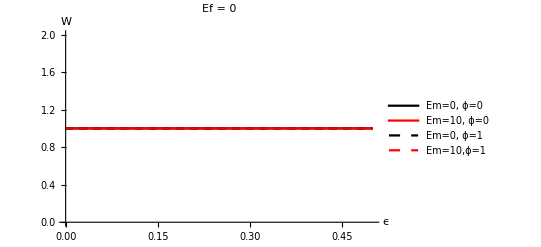

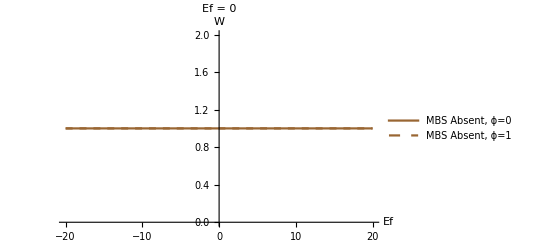

10

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in E0 near {E0} = {-2.65735}. NIntegrate obtained 8.13152×10^-20 and 7.88278×10^-20 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in E0 near {E0} = {3.65488}. NIntegrate obtained 1.65934×10^-18 and 4.48892×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in E0 near {E0} = {-3.4141}. NIntegrate obtained 6.59195×10^-17 and 1.74328×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

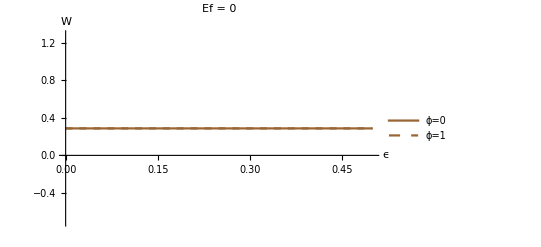

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in E0 near {E0} = {11.1928}. NIntegrate obtained -2.57529×10^-16 and 2.04243×10^-19 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in E0 near {E0} = {12.1309}. NIntegrate obtained -5.35813×10^-16 and 1.36299×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in E0 near {E0} = {11.1928}. NIntegrate obtained -1.53089×10^-16 and 3.69027×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

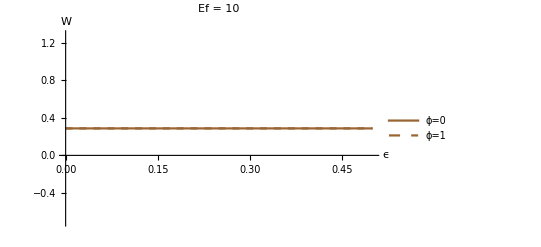

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in E0 near {E0} = {-14.5189}. NIntegrate obtained 2.22045×10^-16 and 2.06418×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
10
Gqe[Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := -Gteoe[Ef,Em,phi,G1]+(Gteue[Ef,Em,phi,G1] ((Gdoeoe[Ef,Em,phi,G1]+Gdohoe[Ef,Em,phi,G1]) (Ldoeie[Ef,Em,phi,G1]+Ldoeoe[Ef,Em,phi,G1]+Ldohie[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1])-(Sdoeoe[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1]) (Sdoeie[Ef,Em,phi,G1]+Sdoeoe[Ef,Em,phi,G1]+Sdohie[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1])))/(-((Grefdoeue[Ef,Em,phi,G1]+Grefdohue[Ef,Em,phi,G1]) (Ldoeie[Ef,Em,phi,G1]+Ldoeoe[Ef,Em,phi,G1]+Ldohie[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1]))+(Sdoeie[Ef,Em,phi,G1]+Sdoeoe[Ef,Em,phi,G1]+Sdohie[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1]) (Srefdoeue[Ef,Em,phi,G1]+Srefdohue[Ef,Em,phi,G1]))-((Grefdoeue[Ef,Em,phi,G1] (Sdoeoe[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1])+Grefdohue[Ef,Em,phi,G1] (Sdoeoe[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1])-(Gdoeoe[Ef,Em,phi,G1]+Gdohoe[Ef,Em,phi,G1]) (Srefdoeue[Ef,Em,phi,G1]+Srefdohue[Ef,Em,phi,G1])) Steue[Ef,Em,phi,G1])/(Grefdoeue[Ef,Em,phi,G1] (Ldoeie[Ef,Em,phi,G1]+Ldoeoe[Ef,Em,phi,G1]+Ldohie[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1])+Grefdohue[Ef,Em,phi,G1] (Ldoeie[Ef,Em,phi,G1]+Ldoeoe[Ef,Em,phi,G1]+Ldohie[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1])-(Sdoeie[Ef,Em,phi,G1]+Sdoeoe[Ef,Em,phi,G1]+Sdohie[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1]) (Srefdoeue[Ef,Em,phi,G1]+Srefdohue[Ef,Em,phi,G1]));

Gqh[ Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] := -Gthoe[Ef,Em,phi,G1]+(Gthue[Ef,Em,phi,G1] ((Gdoeoe[Ef,Em,phi,G1]+Gdohoe[Ef,Em,phi,G1]) (Ldoeie[Ef,Em,phi,G1]+Ldoeoe[Ef,Em,phi,G1]+Ldohie[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1])-(Sdoeoe[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1]) (Sdoeie[Ef,Em,phi,G1]+Sdoeoe[Ef,Em,phi,G1]+Sdohie[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1])))/(-((Grefdoeue[Ef,Em,phi,G1]+Grefdohue[Ef,Em,phi,G1]) (Ldoeie[Ef,Em,phi,G1]+Ldoeoe[Ef,Em,phi,G1]+Ldohie[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1]))+(Sdoeie[Ef,Em,phi,G1]+Sdoeoe[Ef,Em,phi,G1]+Sdohie[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1]) (Srefdoeue[Ef,Em,phi,G1]+Srefdohue[Ef,Em,phi,G1]))-((Grefdoeue[Ef,Em,phi,G1] (Sdoeoe[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1])+Grefdohue[Ef,Em,phi,G1] (Sdoeoe[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1])-(Gdoeoe[Ef,Em,phi,G1]+Gdohoe[Ef,Em,phi,G1]) (Srefdoeue[Ef,Em,phi,G1]+Srefdohue[Ef,Em,phi,G1])) Sthue[Ef,Em,phi,G1])/(Grefdoeue[Ef,Em,phi,G1] (Ldoeie[Ef,Em,phi,G1]+Ldoeoe[Ef,Em,phi,G1]+Ldohie[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1])+Grefdohue[Ef,Em,phi,G1] (Ldoeie[Ef,Em,phi,G1]+Ldoeoe[Ef,Em,phi,G1]+Ldohie[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1])-(Sdoeie[Ef,Em,phi,G1]+Sdoeoe[Ef,Em,phi,G1]+Sdohie[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1]) (Srefdoeue[Ef,Em,phi,G1]+Srefdohue[Ef,Em,phi,G1]));

LheT[ Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=    Lteoe[Ef,Em,phi,G1]+(Lteue[Ef,Em,phi,G1] (Grefdoeue[Ef,Em,phi,G1] (Ldoeoe[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1])+Grefdohue[Ef,Em,phi,G1] (Ldoeoe[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1])-(Sdoeoe[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1]) (Srefdoeue[Ef,Em,phi,G1]+Srefdohue[Ef,Em,phi,G1])))/(Grefdoeue[Ef,Em,phi,G1] (Ldoeie[Ef,Em,phi,G1]+Ldoeoe[Ef,Em,phi,G1]+Ldohie[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1])+Grefdohue[Ef,Em,phi,G1] (Ldoeie[Ef,Em,phi,G1]+Ldoeoe[Ef,Em,phi,G1]+Ldohie[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1])-(Sdoeie[Ef,Em,phi,G1]+Sdoeoe[Ef,Em,phi,G1]+Sdohie[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1]) (Srefdoeue[Ef,Em,phi,G1]+Srefdohue[Ef,Em,phi,G1]))+((Ldoeoe[Ef,Em,phi,G1] (Sdoeie[Ef,Em,phi,G1]+Sdohie[Ef,Em,phi,G1])+Ldohoe[Ef,Em,phi,G1] (Sdoeie[Ef,Em,phi,G1]+Sdohie[Ef,Em,phi,G1])-(Ldoeie[Ef,Em,phi,G1]+Ldohie[Ef,Em,phi,G1]) (Sdoeoe[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1])) Steue[Ef,Em,phi,G1])/(-((Grefdoeue[Ef,Em,phi,G1]+Grefdohue[Ef,Em,phi,G1]) (Ldoeie[Ef,Em,phi,G1]+Ldoeoe[Ef,Em,phi,G1]+Ldohie[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1]))+(Sdoeie[Ef,Em,phi,G1]+Sdoeoe[Ef,Em,phi,G1]+Sdohie[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1]) (Srefdoeue[Ef,Em,phi,G1]+Srefdohue[Ef,Em,phi,G1]));

LhhT[ Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ] :=    Lthoe[Ef,Em,phi,G1]+(Lthue[Ef,Em,phi,G1] (Grefdoeue[Ef,Em,phi,G1] (Ldoeoe[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1])+Grefdohue[Ef,Em,phi,G1] (Ldoeoe[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1])-(Sdoeoe[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1]) (Srefdoeue[Ef,Em,phi,G1]+Srefdohue[Ef,Em,phi,G1])))/(Grefdoeue[Ef,Em,phi,G1] (Ldoeie[Ef,Em,phi,G1]+Ldoeoe[Ef,Em,phi,G1]+Ldohie[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1])+Grefdohue[Ef,Em,phi,G1] (Ldoeie[Ef,Em,phi,G1]+Ldoeoe[Ef,Em,phi,G1]+Ldohie[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1])-(Sdoeie[Ef,Em,phi,G1]+Sdoeoe[Ef,Em,phi,G1]+Sdohie[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1]) (Srefdoeue[Ef,Em,phi,G1]+Srefdohue[Ef,Em,phi,G1]))+((Ldoeoe[Ef,Em,phi,G1] (Sdoeie[Ef,Em,phi,G1]+Sdohie[Ef,Em,phi,G1])+Ldohoe[Ef,Em,phi,G1] (Sdoeie[Ef,Em,phi,G1]+Sdohie[Ef,Em,phi,G1])-(Ldoeie[Ef,Em,phi,G1]+Ldohie[Ef,Em,phi,G1]) (Sdoeoe[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1])) Sthue[Ef,Em,phi,G1])/(-((Grefdoeue[Ef,Em,phi,G1]+Grefdohue[Ef,Em,phi,G1]) (Ldoeie[Ef,Em,phi,G1]+Ldoeoe[Ef,Em,phi,G1]+Ldohie[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1]))+(Sdoeie[Ef,Em,phi,G1]+Sdoeoe[Ef,Em,phi,G1]+Sdohie[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1]) (Srefdoeue[Ef,Em,phi,G1]+Srefdohue[Ef,Em,phi,G1]));


LcT[Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ]:= (Gteue[Ef,Em,phi,G1] (Ldoeoe[Ef,Em,phi,G1] (Sdoeie[Ef,Em,phi,G1]+Sdohie[Ef,Em,phi,G1])+Ldohoe[Ef,Em,phi,G1] (Sdoeie[Ef,Em,phi,G1]+Sdohie[Ef,Em,phi,G1])-(Ldoeie[Ef,Em,phi,G1]+Ldohie[Ef,Em,phi,G1]) (Sdoeoe[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1])))/(-((Grefdoeue[Ef,Em,phi,G1]+Grefdohue[Ef,Em,phi,G1]) (Ldoeie[Ef,Em,phi,G1]+Ldoeoe[Ef,Em,phi,G1]+Ldohie[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1]))+(Sdoeie[Ef,Em,phi,G1]+Sdoeoe[Ef,Em,phi,G1]+Sdohie[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1]) (Srefdoeue[Ef,Em,phi,G1]+Srefdohue[Ef,Em,phi,G1]))+Steoe[Ef,Em,phi,G1]+((Grefdoeue[Ef,Em,phi,G1] (Ldoeoe[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1])+Grefdohue[Ef,Em,phi,G1] (Ldoeoe[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1])-(Sdoeoe[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1]) (Srefdoeue[Ef,Em,phi,G1]+Srefdohue[Ef,Em,phi,G1])) Steue[Ef,Em,phi,G1])/(Grefdoeue[Ef,Em,phi,G1] (Ldoeie[Ef,Em,phi,G1]+Ldoeoe[Ef,Em,phi,G1]+Ldohie[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1])+Grefdohue[Ef,Em,phi,G1] (Ldoeie[Ef,Em,phi,G1]+Ldoeoe[Ef,Em,phi,G1]+Ldohie[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1])-(Sdoeie[Ef,Em,phi,G1]+Sdoeoe[Ef,Em,phi,G1]+Sdohie[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1]) (Srefdoeue[Ef,Em,phi,G1]+Srefdohue[Ef,Em,phi,G1])) + (Gthue[Ef,Em,phi,G1] (Ldoeoe[Ef,Em,phi,G1] (Sdoeie[Ef,Em,phi,G1]+Sdohie[Ef,Em,phi,G1])+Ldohoe[Ef,Em,phi,G1] (Sdoeie[Ef,Em,phi,G1]+Sdohie[Ef,Em,phi,G1])-(Ldoeie[Ef,Em,phi,G1]+Ldohie[Ef,Em,phi,G1]) (Sdoeoe[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1])))/(-((Grefdoeue[Ef,Em,phi,G1]+Grefdohue[Ef,Em,phi,G1]) (Ldoeie[Ef,Em,phi,G1]+Ldoeoe[Ef,Em,phi,G1]+Ldohie[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1]))+(Sdoeie[Ef,Em,phi,G1]+Sdoeoe[Ef,Em,phi,G1]+Sdohie[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1]) (Srefdoeue[Ef,Em,phi,G1]+Srefdohue[Ef,Em,phi,G1]))+Sthoe[Ef,Em,phi,G1]+((Grefdoeue[Ef,Em,phi,G1] (Ldoeoe[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1])+Grefdohue[Ef,Em,phi,G1] (Ldoeoe[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1])-(Sdoeoe[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1]) (Srefdoeue[Ef,Em,phi,G1]+Srefdohue[Ef,Em,phi,G1])) Sthue[Ef,Em,phi,G1])/(Grefdoeue[Ef,Em,phi,G1] (Ldoeie[Ef,Em,phi,G1]+Ldoeoe[Ef,Em,phi,G1]+Ldohie[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1])+Grefdohue[Ef,Em,phi,G1] (Ldoeie[Ef,Em,phi,G1]+Ldoeoe[Ef,Em,phi,G1]+Ldohie[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1])-(Sdoeie[Ef,Em,phi,G1]+Sdoeoe[Ef,Em,phi,G1]+Sdohie[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1]) (Srefdoeue[Ef,Em,phi,G1]+Srefdohue[Ef,Em,phi,G1]))




LqV[Ef_?NumericQ, Em_?NumericQ, phi_?NumericQ,G1_?NumericQ]:=-((Lteue[Ef,Em,phi,G1] (Grefdoeue[Ef,Em,phi,G1] (Sdoeoe[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1])+Grefdohue[Ef,Em,phi,G1] (Sdoeoe[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1])-(Gdoeoe[Ef,Em,phi,G1]+Gdohoe[Ef,Em,phi,G1]) (Srefdoeue[Ef,Em,phi,G1]+Srefdohue[Ef,Em,phi,G1])))/(Grefdoeue[Ef,Em,phi,G1] (Ldoeie[Ef,Em,phi,G1]+Ldoeoe[Ef,Em,phi,G1]+Ldohie[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1])+Grefdohue[Ef,Em,phi,G1] (Ldoeie[Ef,Em,phi,G1]+Ldoeoe[Ef,Em,phi,G1]+Ldohie[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1])-(Sdoeie[Ef,Em,phi,G1]+Sdoeoe[Ef,Em,phi,G1]+Sdohie[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1]) (Srefdoeue[Ef,Em,phi,G1]+Srefdohue[Ef,Em,phi,G1])))-Steoe[Ef,Em,phi,G1]+(((Gdoeoe[Ef,Em,phi,G1]+Gdohoe[Ef,Em,phi,G1]) (Ldoeie[Ef,Em,phi,G1]+Ldoeoe[Ef,Em,phi,G1]+Ldohie[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1])-(Sdoeoe[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1]) (Sdoeie[Ef,Em,phi,G1]+Sdoeoe[Ef,Em,phi,G1]+Sdohie[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1])) Steue[Ef,Em,phi,G1])/(-((Grefdoeue[Ef,Em,phi,G1]+Grefdohue[Ef,Em,phi,G1]) (Ldoeie[Ef,Em,phi,G1]+Ldoeoe[Ef,Em,phi,G1]+Ldohie[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1]))+(Sdoeie[Ef,Em,phi,G1]+Sdoeoe[Ef,Em,phi,G1]+Sdohie[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1]) (Srefdoeue[Ef,Em,phi,G1]+Srefdohue[Ef,Em,phi,G1]))+-((Lthue[Ef,Em,phi,G1] (Grefdoeue[Ef,Em,phi,G1] (Sdoeoe[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1])+Grefdohue[Ef,Em,phi,G1] (Sdoeoe[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1])-(Gdoeoe[Ef,Em,phi,G1]+Gdohoe[Ef,Em,phi,G1]) (Srefdoeue[Ef,Em,phi,G1]+Srefdohue[Ef,Em,phi,G1])))/(Grefdoeue[Ef,Em,phi,G1] (Ldoeie[Ef,Em,phi,G1]+Ldoeoe[Ef,Em,phi,G1]+Ldohie[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1])+Grefdohue[Ef,Em,phi,G1] (Ldoeie[Ef,Em,phi,G1]+Ldoeoe[Ef,Em,phi,G1]+Ldohie[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1])-(Sdoeie[Ef,Em,phi,G1]+Sdoeoe[Ef,Em,phi,G1]+Sdohie[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1]) (Srefdoeue[Ef,Em,phi,G1]+Srefdohue[Ef,Em,phi,G1])))-Sthoe[Ef,Em,phi,G1]+(((Gdoeoe[Ef,Em,phi,G1]+Gdohoe[Ef,Em,phi,G1]) (Ldoeie[Ef,Em,phi,G1]+Ldoeoe[Ef,Em,phi,G1]+Ldohie[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1])-(Sdoeoe[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1]) (Sdoeie[Ef,Em,phi,G1]+Sdoeoe[Ef,Em,phi,G1]+Sdohie[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1])) Sthue[Ef,Em,phi,G1])/(-((Grefdoeue[Ef,Em,phi,G1]+Grefdohue[Ef,Em,phi,G1]) (Ldoeie[Ef,Em,phi,G1]+Ldoeoe[Ef,Em,phi,G1]+Ldohie[Ef,Em,phi,G1]+Ldohoe[Ef,Em,phi,G1]))+(Sdoeie[Ef,Em,phi,G1]+Sdoeoe[Ef,Em,phi,G1]+Sdohie[Ef,Em,phi,G1]+Sdohoe[Ef,Em,phi,G1]) (Srefdoeue[Ef,Em,phi,G1]+Srefdohue[Ef,Em,phi,G1]))


kappa[Ef_,Em_,phi_,G1_]:= (LcV[Ef,Em,phi,G1]*LqT[Ef,Em,phi,G1] - LqV[Ef,Em,phi,G1]*LcT[Ef,Em,phi,G1])(LcV[Ef,Em,phi,G1])


WFLAW[Ef_,Em_,phi_,G1_]:= Abs[(LqT[Ef,Em,phi,G1])/(LcV[Ef, Em, phi, G1])]

LcV[Ef_,Em_,phi_,G1_]:=Gqe[Ef, Em, phi, G1]+Gqh[Ef, Em, phi, G1]
LqT[Ef_,Em_,phi_,G1_]:=LheT[Ef, Em, phi, G1]+LhhT[Ef,Em,phi,G1]

WFLAW[10,    0,1,0.01]
WFLAW[10,  0,1,0.499]
WFLAW[10,10,1,0.01]
WFLAW[10,10,1,0.499]


(*
Plot[{WFLAW[0, 0, 0, 0.5-G], WFLAW[0, 10, 0, 0.5-G], WFLAW[0, 0, 1, 0.5-G], WFLAW[0, 10,1,0.5-G]}, {G, 0,0.499}, PlotPoints->10, MaxRecursion->1,PlotStyle->{{Black,Thick},{Red,Thick},{Black, Dashed,Thick},{Red, Dashed,Thick}},PlotLegends->{"Em=0, ϕ=0","Em=10, ϕ=0","Em=0, ϕ=1","Em=10,ϕ=1"},PlotRange->All, AxesLabel->{"ϵ","W"},PlotLabel->"Ef = 0"]

Plot[{WFLAW[10, 0, 0, 0.5-G], WFLAW[10, 10, 0, 0.5-G], WFLAW[10, 0, 1, 0.5-G], WFLAW[10, 10,1,0.5-G]}, {G, 0,0.499}, PlotPoints->10, MaxRecursion->1,PlotStyle->{{Black,Thick},{Red,Thick},{Black, Dashed,Thick},{Red, Dashed,Thick}},PlotLegends->{"Em=0, ϕ=0","Em=10, ϕ=0","Em=0, ϕ=1","Em=10,ϕ=1"},PlotRange->All, AxesLabel->{"ϵ","W"},PlotLabel->"Ef = 10"]

Plot[{WFLAW[Ef, 0, 0, 0.5 ],  WFLAW[Ef, 0, 1, 0.5]}, {Ef, -20,20}, PlotPoints->10, MaxRecursion->1,PlotStyle->{{Brown,Thick}, {Brown, Dashed, Thick}},PlotLegends->{"MBS Absent, ϕ=0","MBS Absent, ϕ=1"},PlotRange->All, AxesLabel->{"Ef","W"},PlotLabel->"Ef = 0"]

Plot[{WFLAW[0, 0, phi, 0.5],  WFLAW[10, 10, phi, 0.5]}, {phi, -2*Pi,2*Pi}, PlotPoints->10, MaxRecursion->1,PlotStyle->{{Brown,Thick}, {Brown, Dashed, Thick}},PlotLegends->{"MBS Absent, Ef=0","MBS Absent, Ef=10"},PlotRange->All, AxesLabel->{"phi","W"},PlotLabel->"Ef = 10"]
*)
```

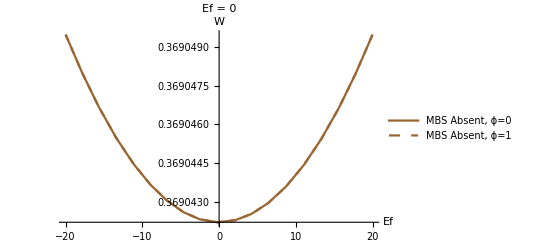

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in E0 near {E0} = {-2.34658}. NIntegrate obtained -1.73472×10^-18 and 6.64237×10^-17 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in E0 near {E0} = {-2.16065}. NIntegrate obtained -2.77556×10^-17 and 1.5056×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in E0 near {E0} = {-3.4141}. NIntegrate obtained 6.59195×10^-17 and 1.74328×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.